```mathematica
ExpressionAsTable[exp_]:=Block[
{},
Table[exp[[k]],{k,1,Length[exp]}]
]
```

## First fix the vertex set for correct color table display

```mathematica
keep=sixNodes["B54"];
```

```mathematica
keep["vertexsets"]=Table[{i},{i,5}]
```

{{1},{2},{3},{4},{5}}

```mathematica
sixNodes["B54"]=keep;
```

```mathematica
keep["compwhy"]
```

Setting the colofour to zero conflicts with known inequalities

## The color table

```mathematica
ColorTablePrint["B54",sixNodes,"colofour3","colortable4"]/.ζ->0
```

-Graphics-B54-α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1Greater
( | = | ≠
1<->2 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
1<->3 | δ1 | -α1-β1+γ-γ1+2 δ-2 δ1+ϵ-ϵ1
1<->4 | β1 | -α1-2 β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
1<->5 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
2<->3 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
2<->4 | -α1+γ | -β1-γ1+2 δ-δ1+ϵ-ϵ1
2<->5 | -β1+2 δ-δ1 | -α1+γ-γ1+ϵ-ϵ1
3<->4 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
3<->5 | ϵ-ϵ1 | -α1-β1+γ-γ1+2 δ-δ1
4<->5 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1)

## The color table for the inner pentagon

```mathematica
ColorTablePrint["full",sixNodes,"colofour3","colortable4"]/.{α1->aa1,β1->bb1,γ1->gg1,δ1->dd1,ϵ1->ee1,ζ->0}//Simplify
```

-Graphics-fullaa1+bb1+dd1+ee1+gg1GreaterEqual
( | = | ≠
1<->2 | 0 | aa1+bb1+dd1+ee1+gg1
1<->3 | aa1+dd1 | bb1+ee1+gg1
1<->4 | bb1+ee1 | aa1+dd1+gg1
1<->5 | 0 | aa1+bb1+dd1+ee1+gg1
2<->3 | 0 | aa1+bb1+dd1+ee1+gg1
2<->4 | aa1+gg1 | bb1+dd1+ee1
2<->5 | bb1+dd1 | aa1+ee1+gg1
3<->4 | 0 | aa1+bb1+dd1+ee1+gg1
3<->5 | ee1+gg1 | aa1+bb1+dd1
4<->5 | 0 | aa1+bb1+dd1+ee1+gg1)

If we rename the “1” in the inner pentagon to 7, we have still some color relations that are shared, namely for 2<->5, 3<->5 and 2<->4:

```mathematica
Reduce[{-β1+2 δ-δ1==bb1+dd1,-α1+γ-γ1+ϵ-ϵ1==aa1+ee1+gg1,ϵ-ϵ1==ee1+gg1,-α1-β1+γ-γ1+2 δ-δ1==aa1+bb1+dd1,-α1+γ==aa1+gg1,-β1-γ1+2 δ-δ1+ϵ-ϵ1==bb1+dd1+ee1},{α1,β1,γ1,δ1,ϵ1}]
```

α1==-aa1-gg1+γ&&γ1==gg1&&δ1==-bb1-dd1-β1+2 δ&&ϵ1==-ee1-gg1+ϵ

```mathematica
Reduce[{-β1+2 δ-δ1==bb1+dd1,-α1+γ-γ1+ϵ-ϵ1==aa1+ee1+gg1,ϵ-ϵ1==ee1+gg1,-α1-β1+γ-γ1+2 δ-δ1==aa1+bb1+dd1,-α1+γ==aa1+gg1,-β1-γ1+2 δ-δ1+ϵ-ϵ1==bb1+dd1+ee1},{aa1,bb1,gg1,dd1,ee1}]
```

aa1==-α1+γ-γ1&&gg1==γ1&&dd1==-bb1-β1+2 δ-δ1&&ee1==-γ1+ϵ-ϵ1

```mathematica
Reduce[{aa1+2dd1+ee1==x,aa1==-α1+γ-γ1&&gg1==γ1&&dd1==-bb1-β1+2 δ-δ1&&ee1==-γ1+ϵ-ϵ1},x]
```

gg1==γ1&&ee1==-γ1+ϵ-ϵ1&&bb1==-dd1-β1+2 δ-δ1&&aa1==-α1+γ-γ1&&x==2 dd1-α1+γ-2 γ1+ϵ-ϵ1

```mathematica
Reduce[β1+ϵ<ee1+gg1+β&&ee1==-γ1+ϵ-ϵ1,{gg1,ee1}]
```

(β|β1|ϵ)∈Reals&&Im[γ1]==-Im[ϵ1]&&gg1>-β+β1+Re[γ1]+Re[ϵ1]&&ee1==-γ1+ϵ-ϵ1

```mathematica
Reduce[β1+ϵ<ee1+gg1+β&&ee1==-γ1+ϵ-ϵ1,{gg1,γ1}]
```

(ee1|β|β1|ϵ)∈Reals&&gg1>-ee1-β+β1+ϵ&&γ1==-ee1+ϵ-ϵ1

```mathematica
Reduce[{-β1+2 δ-δ1==bb1+dd1,-α1+γ-γ1+ϵ-ϵ1==aa1+ee1+gg1,ϵ-ϵ1==ee1+gg1,-α1-β1+γ-γ1+2 δ-δ1==aa1+bb1+dd1,-α1+γ==aa1+gg1,-β1-γ1+2 δ-δ1+ϵ-ϵ1==bb1+dd1+ee1},{δ1}]
```

gg1==γ1&&ee1==-γ1+ϵ-ϵ1&&aa1==-α1+γ-γ1&&δ1==-bb1-dd1-β1+2 δ

## The color table

```mathematica
ColorTablePrint["Q02",sixNodes,"colofour3","colortable4"]/.ζ->0
```

-Graphics-Q02γ+2 δ+ϵGreater
( | = | ≠
1<->2 | 0 | γ+2 δ+ϵ
 | α1+2 δ1 | -α1+γ+2 δ-2 δ1+ϵ
 | 2 β1+ϵ1 | -2 β1+γ+2 δ+ϵ-ϵ1
 | 0 | γ+2 δ+ϵ
 | 0 | γ+2 δ+ϵ
 | γ+γ1 | -γ1+2 δ+ϵ
 | 2 δ | γ+ϵ
 | 0 | γ+2 δ+ϵ
 | γ1+ϵ | γ-γ1+2 δ
 | 0 | γ+2 δ+ϵ)

```mathematica
ColorTablePrint["B18",sixNodes,"colofour3","colortable4"]/.{α1->aa1,β1->bb1,γ1->gg1,δ1->dd1,ϵ1->ee1,γ->gg,δ->dd,ϵ->ee,ζ->0}
```

-Graphics-B18dd+ee+ggGreater
( | = | ≠
1<->2 | 0 | dd+ee+gg
 | aa1+dd1 | -aa1+dd-dd1+ee+gg
 | bb1+ee1 | -bb1+dd+ee-ee1+gg
 | 0 | dd+ee+gg
 | 0 | dd+ee+gg
 | gg+gg1 | dd+ee-gg1
 | dd | ee+gg
 | 0 | dd+ee+gg
 | ee+gg1 | dd+gg-gg1
 | 0 | dd+ee+gg)

```mathematica
Reduce[{gg+gg1==γ+γ1,dd==2 δ,ee+gg1==γ1+ϵ,-γ1+2 δ+ϵ==dd+ee-gg1,γ+ϵ==ee+gg,γ-γ1+2 δ==dd+gg-gg1},{α1,β1,γ1,δ1,ϵ1}]
```

gg==γ&&ee==ϵ&&dd==2 δ&&γ1==gg1

```mathematica
Reduce[{gg+gg1==γ+γ1,dd==2 δ,ee+gg1==γ1+ϵ,-γ1+2 δ+ϵ==dd+ee-gg1,γ+ϵ==ee+gg,γ-γ1+2 δ==dd+gg-gg1},{aa1,bb1,gg1,dd1,ee1}]
```

gg==γ&&ee==ϵ&&dd==2 δ&&gg1==γ1

## All together now

```mathematica
Reduce[{gg+gg1==γ+γ1,dd==2 δ,ee+gg1==γ1+ϵ,-γ1+2 δ+ϵ==dd+ee-gg1,γ+ϵ==ee+gg,γ-γ1+2 δ==dd+gg-gg1,

-β1+2 δ-δ1==bb1+dd1,-α1+γ-γ1+ϵ-ϵ1==aa1+ee1+gg1,ϵ-ϵ1==ee1+gg1,-α1-β1+γ-γ1+2 δ-δ1==aa1+bb1+dd1,-α1+γ==aa1+gg1,-β1-γ1+2 δ-δ1+ϵ-ϵ1==bb1+dd1+ee1
},{α1,β1,γ1,δ1,ϵ1,γ,ϵ}]
```

dd==2 δ&&α1==-aa1+gg-gg1&&γ1==gg1&&δ1==-bb1-dd1-β1+2 δ&&ϵ1==ee-ee1-gg1&&γ==gg&&ϵ==ee

```mathematica
Reduce[{gg+gg1==γ+γ1,dd==2 δ,ee+gg1==γ1+ϵ,-γ1+2 δ+ϵ==dd+ee-gg1,γ+ϵ==ee+gg,γ-γ1+2 δ==dd+gg-gg1,

-β1+2 δ-δ1==bb1+dd1,-α1+γ-γ1+ϵ-ϵ1==aa1+ee1+gg1,ϵ-ϵ1==ee1+gg1,-α1-β1+γ-γ1+2 δ-δ1==aa1+bb1+dd1,-α1+γ==aa1+gg1,-β1-γ1+2 δ-δ1+ϵ-ϵ1==bb1+dd1+ee1
},{aa1,bb1,gg1,dd1,ee1,dd,ee}]
```

gg==γ&&aa1==-α1+γ-γ1&&gg1==γ1&&dd1==-bb1-β1+2 δ-δ1&&ee1==-γ1+ϵ-ϵ1&&dd==2 δ&&ee==ϵ

## Full color table

```mathematica
ColorTablePrint["full",sixNodes,"colofour3","colortable4"]/.{α1->aa1,β1->bb1,γ1->gg1,δ1->dd1,ϵ1->ee1,ζ->0}
```

-Graphics-fullaa1+bb1+dd1+ee1+gg1GreaterEqual
( | = | ≠
1<->2 | 0 | aa1+bb1+dd1+ee1+gg1
1<->3 | aa1+dd1 | bb1+ee1+gg1
1<->4 | bb1+ee1 | aa1+dd1+gg1
1<->5 | 0 | aa1+bb1+dd1+ee1+gg1
2<->3 | 0 | aa1+bb1+dd1+ee1+gg1
2<->4 | aa1+gg1 | bb1+dd1+ee1
2<->5 | bb1+dd1 | aa1+ee1+gg1
3<->4 | 0 | aa1+bb1+dd1+ee1+gg1
3<->5 | ee1+gg1 | aa1+bb1+dd1
4<->5 | 0 | aa1+bb1+dd1+ee1+gg1)

```mathematica
shortFormulas=Select[ExpressionAsTable[ineqsix2],Length[#[[1]]]==2&&Length[#[[2]]]<3&]/.ζ->0;Length[shortFormulas]
```

20

```mathematica
shortFormulas
```

{s02+s17>0,s04+s10>0,s03+s16>0,s05+s09>0,γ1+ϵ1<ϵ,β1+δ1<δ,α1+γ1<γ,β1+ϵ1<β,s05+s19>0,s04+s20>0,α1+δ1<α,s03+s08>0,s02+s07>0,s01+s18>0,s01+s06>0}

```mathematica
more=Simplify[(Fold[And,shortFormulas])/.{α1-> -aa1-gg1+γ,γ1->gg1,δ1->-bb1-dd1-β1+2 δ,ϵ1->-ee1-gg1+ϵ}];Length[more]
```

20

```mathematica
more[[1]]
```

s02+s17>0

```mathematica
ExpressionToTable2[more]
```

aa1>0
ee1>0
s01+s06>0
s01+s18>0
s02+s07>0
s02+s17>0
s03+s08>0
s03+s16>0
s04+s10>0
s04+s20>0
s05+s09>0
s05+s19>0
δ<bb1+dd1
b01+b06<b16+z
b02+b07<b17+z
b03+b08<b18+z
b04+b09<b19+z
b05+b10<b20+z
β1+ϵ<ee1+gg1+β
γ+2 δ<aa1+bb1+dd1+gg1+α+β1

```mathematica
TableForm[Sort[Table[sixNodes[key]["colofour3"],{key,Select[Keys[sixNodes],ToString[sixNodes[#]["comp"]]≠"Greater"&]}]]]
```

s01
s02
s03
s04
s05
s06
s07
s08
s09
s10
s11
s12
s13
s14
s15
s16
s17
s18
s19
s20
α1
s03+α1
s04+α1
s03+s04+α1
β1
s02+β1
s05+β1
s02+s05+β1
γ1
s01+γ1
s03+γ1
s01+s03+γ1
δ1
s02+δ1
s04+δ1
s02+s04+δ1
ϵ1
s01+ϵ1
s05+ϵ1
s01+s05+ϵ1
s11-ζ
s12-ζ
s11+s12-ζ
s13-ζ
s12+s13-ζ
s14-ζ
s11+s14-ζ
s15-ζ
s13+s15-ζ
s14+s15-ζ
α1+β1+γ1+δ1+ϵ1-ζ
ζ

```mathematica
nozeta=Simplify[ineqsix2/.ζ->0];Length[nozeta]
```

898

```mathematica
ExpressionToTable[nozeta]
```

1
 |  |  |  |

```mathematica
Select[ExpressionAsTable[ineqsix2],Length[#[[1]]]<3&&Length[#[[2]]]<3&]
```

{z>0,b06>0,b04>0,b01>0,b02>0,b03>0,b05>0,b14>0,b16>0,b17>0,b18>0,b19>0,b20>0,s01≥0,s03≥0,s05≥0,s06≥0,s07≥0,s08≥0,s09≥0,s10≥0,s11≥0,s12≥0,s13≥0,s14≥0,s15≥0,s16≥0,s17≥0,s18≥0,s19≥0,s20≥0,α>0,α1≥0,β>0,β1≥0,γ>0,γ1≥0,δ>0,δ1≥0,ϵ>0,ϵ1≥0,ζ≥0,b07>0,b12>0,b15>0,s04≥0,b08>0,b10>0,b13>0,s02≥0,b11>0,b09>0,b06<z,b04<z,b07<z,b17<b02,b02<z,b02+b07<b17+z,b12<b05,b05<z,b12<b04,b08<z,b10<z,b20<b05,b05+b10<b20+z,b11<b03,b15<b03,b18<b03,b03<z,b11<b04,b15<b02,b03+b08<b18+z,b16<b01,b14<b01,b13<b01,b01<z,b01+b06<b16+z,b14<b02,b13<b05,ζ<s07+s12,s02+s17>0,ζ<s11+s20,s04+s10>0,ζ<s08+s14,s03+s16>0,ζ<s13+s19,s05+s09>0,ζ<s10+s11,ζ<s12+s17,ζ≤s11,γ1+ϵ1<ϵ,ζ≤s12,β1+δ1<δ,α1+γ1<γ,ζ<s09+s13,ζ≤s13,ζ<s14+s16,ζ≤s14,β1+ϵ1<β,s05+s19>0,s04+s20>0,α1+δ1<α,s03+s08>0,s02+s07>0,b09<z,b19<b04,b04+b09<b19+z,ζ<s06+s15,s01+s18>0,ζ<s15+s18,ζ≤s15,s01+s06>0}

```mathematica
ExpressionToTable2[ineqsix2]
```

1
 |  |  |  |

## Testing the hypothesis by embedding the graph inside plantri 2

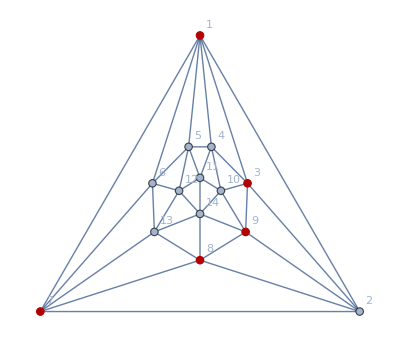

```mathematica
g10000=Graph[plantri[[2]],GraphLayout->"TutteEmbedding",VertexLabels->"Name",GraphHighlight->{7,8,9,3,1}]
```

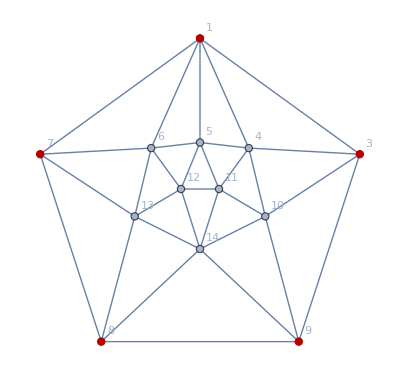

```mathematica
baseGraph=VertexDelete[g10000,2]
```

```mathematica
solsBase=GraphSolutions2[baseGraph];
```

```mathematica
Map[{SymbolToKey[#[[1]]],#[[2]]}&,{x1->1,x2->2,x3->3}]
```

{{1,1},{2,2},{3,3}}

```mathematica
Map[Map[{SymbolToKey[#[[1]]],#[[2]]}&,#]&,Out[428]]
```

%428

```mathematica
ColorTable[g_]:=Block[{sols=GraphSolutions2[g], transformed, same, different,vector, size=VertexCount[g]},
Print["solutions computed"];
Print[sols[[1]]];
transformed= Map[Map[{SymbolToKey[#[[1]]],#[[2]]}&,#]&,sols];
same=Table[0,{i,size},{j,size}];
different=Table[0,{i,size},{j,size}];
Table[
vector=Table[0,{i,size}];
Table[vector[[assignment[[1]] ]]=assignment[[2]],
{assignment,s}
];
Table[If[vector[[i]]==vector[[j]],
same[[i,j]]=same[[i,j]]+1;
same[[j,i]]=same[[j,i]]+1,
different[[i,j]]=different[[i,j]]+1;
different[[j,i]]=different[[j,i]]+1
],{i,Length[vector]},{j,Length[vector]}]
,{s,transformed}];
{"same"->same/24,"differen"->different/24}
]
```

```mathematica
{c2<->a,c3<->a,c4<->a,c5<->a,c1<->b,c2<->b,a<->b,c5<->b}/.{c1->1,c2->3,c3->9,c4->8,c5->7,a->2,b->15}
```

{3<->2,9<->2,8<->2,7<->2,1<->15,3<->15,2<->15,7<->15}

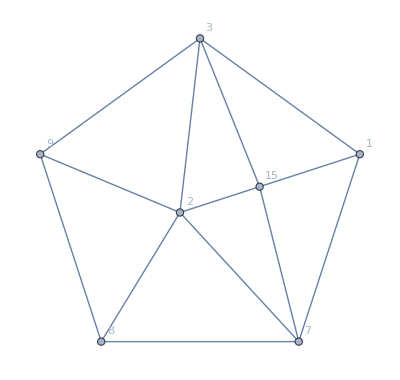

```mathematica
EdgeAdd[Graph[{c2<->a,c3<->a,c4<->a,c5<->a,c1<->b,c2<->b,a<->b,c5<->b}/.{c1->1,c2->3,c3->9,c4->8,c5->7,a->2,b->15},VertexLabels->"Name", GraphLayout->"TutteEmbedding"],{1<->3,3<->9,9<->8,8<->7,7<->1}]
```

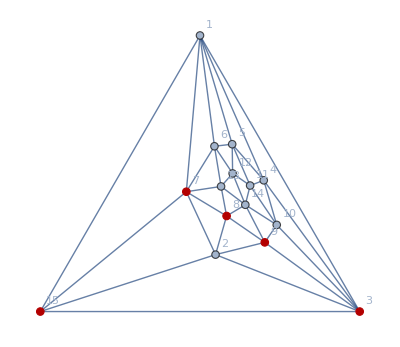

```mathematica
problem=Graph[EdgeList[EdgeAdd[baseGraph,{c2<->a,c3<->a,c4<->a,c5<->a,c1<->b,c2<->b,a<->b,c5<->b}/.{c1->1,c2->3,c3->9,c4->8,c5->7,a->2,b->15}]],VertexLabels->"Name",GraphLayout->"TutteEmbedding",GraphHighlight->{7,8,9,3,15}]
```

```mathematica
ColorTable[g10000]
```

solutions computed

{x1→1,x2→2,x3→3,x4→2,x5→3,x6→2,x7→3,x8→1,x9→4,x10→1,x11→4,x12→1,x13→4,x14→2}

{same→{{40,0,0,0,0,0,0,18,18,18,18,18,18,2},{0,40,0,24,8,24,0,0,0,10,4,4,10,18},{0,0,40,0,24,8,24,10,0,0,10,4,4,18},{0,24,0,40,0,24,8,4,10,0,0,10,4,18},{0,8,24,0,40,0,24,4,4,10,0,0,10,18},{0,24,8,24,0,40,0,10,4,4,10,0,0,18},{0,0,24,8,24,0,40,0,10,4,4,10,0,18},{18,0,10,4,4,10,0,40,0,24,8,24,0,0},{18,0,0,10,4,4,10,0,40,0,24,8,24,0},{18,10,0,0,10,4,4,24,0,40,0,24,8,0},{18,4,10,0,0,10,4,8,24,0,40,0,24,0},{18,4,4,10,0,0,10,24,8,24,0,40,0,0},{18,10,4,4,10,0,0,0,24,8,24,0,40,0},{2,18,18,18,18,18,18,0,0,0,0,0,0,40}},differen→{{0,40,40,40,40,40,40,22,22,22,22,22,22,38},{40,0,40,16,32,16,40,40,40,30,36,36,30,22},{40,40,0,40,16,32,16,30,40,40,30,36,36,22},{40,16,40,0,40,16,32,36,30,40,40,30,36,22},{40,32,16,40,0,40,16,36,36,30,40,40,30,22},{40,16,32,16,40,0,40,30,36,36,30,40,40,22},{40,40,16,32,16,40,0,40,30,36,36,30,40,22},{22,40,30,36,36,30,40,0,40,16,32,16,40,40},{22,40,40,30,36,36,30,40,0,40,16,32,16,40},{22,30,40,40,30,36,36,16,40,0,40,16,32,40},{22,36,30,40,40,30,36,32,16,40,0,40,16,40},{22,36,36,30,40,40,30,16,32,16,40,0,40,40},{22,30,36,36,30,40,40,40,16,32,16,40,0,40},{38,22,22,22,22,22,22,40,40,40,40,40,40,0}}}

```mathematica
ColorTable[problem]
```

solutions computed

{x1→1,x2→4,x3→2,x4→3,x5→2,x6→3,x7→2,x8→3,x9→1,x10→4,x11→1,x12→4,x13→1,x14→2,x15→3}

{same→{{64,40,0,0,0,0,0,12,12,38,24,24,38,2,0},{40,64,0,16,0,16,0,0,0,30,16,16,30,10,0},{0,0,64,0,48,12,48,10,0,0,12,2,0,46,0},{0,16,0,64,0,24,12,12,34,0,0,28,10,10,24},{0,0,48,0,64,0,48,4,4,6,0,0,6,50,12},{0,16,12,24,0,64,0,34,12,10,28,0,0,10,24},{0,0,48,12,48,0,64,0,10,0,2,12,0,46,0},{12,0,10,12,4,34,0,64,0,32,20,26,0,0,30},{12,0,0,34,4,12,10,0,64,0,26,20,32,0,30},{38,30,0,0,6,10,0,32,0,64,0,34,16,0,18},{24,16,12,0,0,28,2,20,26,0,64,0,34,0,16},{24,16,2,28,0,0,12,26,20,34,0,64,0,0,16},{38,30,0,10,6,0,0,0,32,16,34,0,64,0,18},{2,10,46,10,50,10,46,0,0,0,0,0,0,64,2},{0,0,0,24,12,24,0,30,30,18,16,16,18,2,64}},differen→{{0,24,64,64,64,64,64,52,52,26,40,40,26,62,64},{24,0,64,48,64,48,64,64,64,34,48,48,34,54,64},{64,64,0,64,16,52,16,54,64,64,52,62,64,18,64},{64,48,64,0,64,40,52,52,30,64,64,36,54,54,40},{64,64,16,64,0,64,16,60,60,58,64,64,58,14,52},{64,48,52,40,64,0,64,30,52,54,36,64,64,54,40},{64,64,16,52,16,64,0,64,54,64,62,52,64,18,64},{52,64,54,52,60,30,64,0,64,32,44,38,64,64,34},{52,64,64,30,60,52,54,64,0,64,38,44,32,64,34},{26,34,64,64,58,54,64,32,64,0,64,30,48,64,46},{40,48,52,64,64,36,62,44,38,64,0,64,30,64,48},{40,48,62,36,64,64,52,38,44,30,64,0,64,64,48},{26,34,64,54,58,64,64,64,32,48,30,64,0,64,46},{62,54,18,54,14,54,18,64,64,64,64,64,64,0,62},{64,64,64,40,52,40,64,34,34,46,48,48,46,62,0}}}

```mathematica
Graph[problem,GraphLayout->"SpringElectricalEmbedding"]//EdgeList//Sort
```

{1<->3,1<->4,1<->5,1<->6,1<->7,1<->15,2<->15,3<->2,3<->4,3<->9,3<->10,3<->15,4<->5,4<->10,4<->11,5<->6,5<->11,5<->12,6<->7,6<->12,6<->13,7<->2,7<->8,7<->13,7<->15,8<->2,8<->9,8<->13,8<->14,9<->2,9<->10,9<->14,10<->11,10<->14,11<->12,11<->14,12<->13,12<->14,13<->14}

```mathematica
{c2<->a,c3<->a,c4<->a,c5<->a,c1<->b,c2<->b,a<->b,c5<->b}/.{c1->1,c2->3,c3->9,c4->8,c5->7,a->2,b->15}
```

{3<->2,9<->2,8<->2,7<->2,1<->15,3<->15,2<->15,7<->15}

```mathematica
ColorTable[problem]
```

solutions computed

{x1→1,x2→4,x3→2,x4→3,x5→2,x6→3,x7→2,x8→3,x9→1,x10→4,x11→1,x12→4,x13→1,x14→2,x15→3}

{same→{{64,40,0,0,0,0,0,12,12,38,24,24,38,2,0},{40,64,0,16,0,16,0,0,0,30,16,16,30,10,0},{0,0,64,0,48,12,48,10,0,0,12,2,0,46,0},{0,16,0,64,0,24,12,12,34,0,0,28,10,10,24},{0,0,48,0,64,0,48,4,4,6,0,0,6,50,12},{0,16,12,24,0,64,0,34,12,10,28,0,0,10,24},{0,0,48,12,48,0,64,0,10,0,2,12,0,46,0},{12,0,10,12,4,34,0,64,0,32,20,26,0,0,30},{12,0,0,34,4,12,10,0,64,0,26,20,32,0,30},{38,30,0,0,6,10,0,32,0,64,0,34,16,0,18},{24,16,12,0,0,28,2,20,26,0,64,0,34,0,16},{24,16,2,28,0,0,12,26,20,34,0,64,0,0,16},{38,30,0,10,6,0,0,0,32,16,34,0,64,0,18},{2,10,46,10,50,10,46,0,0,0,0,0,0,64,2},{0,0,0,24,12,24,0,30,30,18,16,16,18,2,64}},differen→{{0,24,64,64,64,64,64,52,52,26,40,40,26,62,64},{24,0,64,48,64,48,64,64,64,34,48,48,34,54,64},{64,64,0,64,16,52,16,54,64,64,52,62,64,18,64},{64,48,64,0,64,40,52,52,30,64,64,36,54,54,40},{64,64,16,64,0,64,16,60,60,58,64,64,58,14,52},{64,48,52,40,64,0,64,30,52,54,36,64,64,54,40},{64,64,16,52,16,64,0,64,54,64,62,52,64,18,64},{52,64,54,52,60,30,64,0,64,32,44,38,64,64,34},{52,64,64,30,60,52,54,64,0,64,38,44,32,64,34},{26,34,64,64,58,54,64,32,64,0,64,30,48,64,46},{40,48,52,64,64,36,62,44,38,64,0,64,30,64,48},{40,48,62,36,64,64,52,38,44,30,64,0,64,64,48},{26,34,64,54,58,64,64,64,32,48,30,64,0,64,46},{62,54,18,54,14,54,18,64,64,64,64,64,64,0,62},{64,64,64,40,52,40,64,34,34,46,48,48,46,62,0}}}

```mathematica
EdgeList[-Graphics-]
```

{1<->2,2<->3,3<->4,4<->5,5<->1,2<->6,3<->6,4<->6,5<->6,1<->7,2<->7,6<->7,5<->7}

```mathematica
{c2<->a,c3<->a,c4<->a,c5<->a,c1<->b,c2<->b,a<->b,c5<->b}
```

```mathematica
ExtractSubMatrix[matrix_,list_]:=Block[{result},
result=Table[matrix[[list[[i]],list[[j]]]],{i,5},{j,5}]
]
```

```mathematica
same={{64,40,0,0,0,0,0,12,12,38,24,24,38,2,0},{40,64,0,16,0,16,0,0,0,30,16,16,30,10,0},{0,0,64,0,48,12,48,10,0,0,12,2,0,46,0},{0,16,0,64,0,24,12,12,34,0,0,28,10,10,24},{0,0,48,0,64,0,48,4,4,6,0,0,6,50,12},{0,16,12,24,0,64,0,34,12,10,28,0,0,10,24},{0,0,48,12,48,0,64,0,10,0,2,12,0,46,0},{12,0,10,12,4,34,0,64,0,32,20,26,0,0,30},{12,0,0,34,4,12,10,0,64,0,26,20,32,0,30},{38,30,0,0,6,10,0,32,0,64,0,34,16,0,18},{24,16,12,0,0,28,2,20,26,0,64,0,34,0,16},{24,16,2,28,0,0,12,26,20,34,0,64,0,0,16},{38,30,0,10,6,0,0,0,32,16,34,0,64,0,18},{2,10,46,10,50,10,46,0,0,0,0,0,0,64,2},{0,0,0,24,12,24,0,30,30,18,16,16,18,2,64}};
```

```mathematica
different={{0,24,64,64,64,64,64,52,52,26,40,40,26,62,64},{24,0,64,48,64,48,64,64,64,34,48,48,34,54,64},{64,64,0,64,16,52,16,54,64,64,52,62,64,18,64},{64,48,64,0,64,40,52,52,30,64,64,36,54,54,40},{64,64,16,64,0,64,16,60,60,58,64,64,58,14,52},{64,48,52,40,64,0,64,30,52,54,36,64,64,54,40},{64,64,16,52,16,64,0,64,54,64,62,52,64,18,64},{52,64,54,52,60,30,64,0,64,32,44,38,64,64,34},{52,64,64,30,60,52,54,64,0,64,38,44,32,64,34},{26,34,64,64,58,54,64,32,64,0,64,30,48,64,46},{40,48,52,64,64,36,62,44,38,64,0,64,30,64,48},{40,48,62,36,64,64,52,38,44,30,64,0,64,64,48},{26,34,64,54,58,64,64,64,32,48,30,64,0,64,46},{62,54,18,54,14,54,18,64,64,64,64,64,64,0,62},{64,64,64,40,52,40,64,34,34,46,48,48,46,62,0}};
```

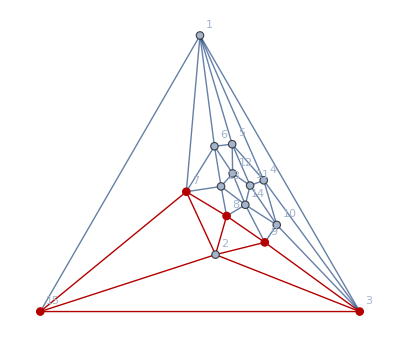

```mathematica
Graph[problem,GraphHighlight->{3<->9,9<->8,8<->7,7<->15,15<->3,3<->2,9<->2,8<->2,7<->2,15<->2}]
```

```mathematica
ExtractSubMatrix[same,{7,8,9,3,15}]//TableForm
```

64 | 0 | 10 | 48 | 0
0 | 64 | 0 | 10 | 30
10 | 0 | 64 | 0 | 30
48 | 10 | 0 | 64 | 0
0 | 30 | 30 | 0 | 64

```mathematica
Solve[{aa1+dd1==10,bb1+ee1==48,aa1+gg1==10,bb1+dd1==30,ee1+gg1==30}]
```

{{aa1→4,bb1→24,dd1→6,ee1→24,gg1→6}}

```mathematica
ExtractSubMatrix[different,{7,8,9,3,15}]//TableForm
```

0 | 64 | 54 | 16 | 64
64 | 0 | 64 | 54 | 34
54 | 64 | 0 | 64 | 34
16 | 54 | 64 | 0 | 64
64 | 34 | 34 | 64 | 0

```mathematica
Solve[{bb1+ee1+gg1==54,aa1+dd1+gg1==16,bb1+dd1+ee1==54,aa1+ee1+gg1==34,aa1+bb1+dd1==34}]
```

{{aa1→4,bb1→24,dd1→6,ee1→24,gg1→6}}

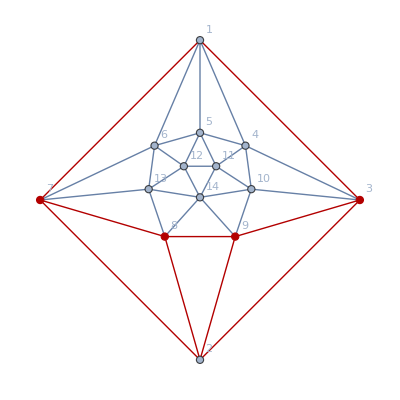

```mathematica
VertexDelete[Graph[problem,GraphHighlight->{3<->9,9<->8,8<->7,7<->1,1<->3,3<->2,9<->2,8<->2,7<->2,1<->2}],15]
```

```mathematica
ExtractSubMatrix[same,{1,7,8,9,3}]//TableForm
```

64 | 0 | 12 | 12 | 0
0 | 64 | 0 | 10 | 48
12 | 0 | 64 | 0 | 10
12 | 10 | 0 | 64 | 0
0 | 48 | 10 | 0 | 64

```mathematica
Solve[{δ1==12,β1==12,-α1+γ==10,-β1+2 δ-δ1==48,ϵ-ϵ1==10}]
```

{{β1→12,γ→10+α1,δ→36,δ1→12,ϵ1→-10+ϵ}}

```mathematica
ExtractSubMatrix[different,{3,1,7,8,9}]//TableForm
```

0 | 64 | 16 | 54 | 64
64 | 0 | 64 | 52 | 52
16 | 64 | 0 | 64 | 54
54 | 52 | 64 | 0 | 64
64 | 52 | 54 | 64 | 0

```mathematica
ExtractSubMatrix[different,{7,8,9,3,1}]//TableForm
```

0 | 64 | 54 | 16 | 64
64 | 0 | 64 | 54 | 52
54 | 64 | 0 | 64 | 52
16 | 54 | 64 | 0 | 64
64 | 52 | 52 | 64 | 0

```mathematica
Solve[{bb1+ee1+gg1==54,aa1+dd1+gg1==16,bb1+dd1+ee1==54,aa1+ee1+gg1==52,aa1+bb1+dd1==52}]
```

{{aa1→28,bb1→30,dd1→-6,ee1→30,gg1→-6}}

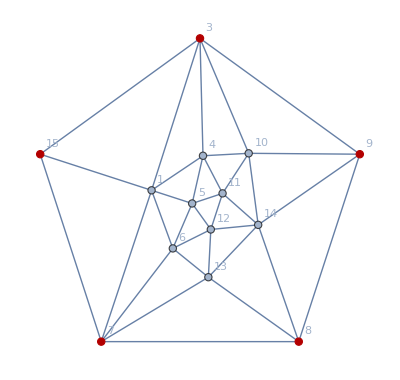

```mathematica
VertexDelete[problem,2]
```

## Now make sure you get the vertices right (top must be top, clockwise must be clockwise ...)

```mathematica
ExtractSubMatrix[same,{1,7,8,9,3}]//TableForm
```

64 | 0 | 12 | 12 | 0
0 | 64 | 0 | 10 | 48
12 | 0 | 64 | 0 | 10
12 | 10 | 0 | 64 | 0
0 | 48 | 10 | 0 | 64

```mathematica
Solve[{δ1==12,β1==12,-α1+γ==10,-β1+2 δ-δ1==48,ϵ-ϵ1==10}]
```

{{β1→12,γ→10+α1,δ→36,δ1→12,ϵ1→-10+ϵ}}

```mathematica
ExtractSubMatrix[different,{1,7,8,9,3}]//TableForm
```

0 | 64 | 52 | 52 | 64
64 | 0 | 64 | 54 | 16
52 | 64 | 0 | 64 | 54
52 | 54 | 64 | 0 | 64
64 | 16 | 54 | 64 | 0

```mathematica
Solve[{-α1-β1+γ-γ1+2 δ-2 δ1+ϵ-ϵ1==52,-α1-2 β1+γ-γ1+2 δ-δ1+ϵ-ϵ1==52,-β1-γ1+2 δ-δ1+ϵ-ϵ1==54,-α1+γ-γ1+ϵ-ϵ1==16,-α1-β1+γ-γ1+2 δ-δ1==54}]
```

{{γ→-2+α1+β1,γ1→-20+2 β1,δ→18+(3 β1)/2,δ1→β1,ϵ1→2-β1+ϵ}}

```mathematica
Solve[{δ1==12,β1==12,-α1+γ==10,-β1+2 δ-δ1==48,ϵ-ϵ1==10,

-α1-β1+γ-γ1+2 δ-2 δ1+ϵ-ϵ1==52,-α1-2 β1+γ-γ1+2 δ-δ1+ϵ-ϵ1==52,-β1-γ1+2 δ-δ1+ϵ-ϵ1==54,-α1+γ-γ1+ϵ-ϵ1==16,-α1-β1+γ-γ1+2 δ-δ1==54}]
```

{{β1→12,γ→10+α1,γ1→4,δ→36,δ1→12,ϵ1→-10+ϵ}}

```mathematica
ExtractSubMatrix[same,{15,7,8,9,3}]//TableForm
```

64 | 0 | 30 | 30 | 0
0 | 64 | 0 | 10 | 48
30 | 0 | 64 | 0 | 10
30 | 10 | 0 | 64 | 0
0 | 48 | 10 | 0 | 64

```mathematica
Solve[{aa1+dd1==30,bb1+ee1==30,aa1+gg1==10,bb1+dd1==48,ee1+gg1==10}]
```

{{aa1→6,bb1→24,dd1→24,ee1→6,gg1→4}}

```mathematica
ExtractSubMatrix[different,{15,7,8,9,3}]//TableForm
```

0 | 64 | 34 | 34 | 64
64 | 0 | 64 | 54 | 16
34 | 64 | 0 | 64 | 54
34 | 54 | 64 | 0 | 64
64 | 16 | 54 | 64 | 0

```mathematica
Solve[{bb1+ee1+gg1==34,aa1+dd1+gg1==34,bb1+dd1+ee1==54,aa1+ee1+gg1==16,aa1+bb1+dd1==54}]
```

{{aa1→6,bb1→24,dd1→24,ee1→6,gg1→4}}

```mathematica
ineqsix2/.{aa1->6,bb1->24,dd1->24,ee1->6,gg1->4}/.{β1->12,γ->10+α1,γ1->4,δ->36,δ1->12,ϵ1->-10+ϵ}//Simplify//ExpressionAsTable//TableForm
```

z>0
b06>0
b04>0
b01>0
b02>0
b03>0
b05>0
b14>0
b16>0
b17>0
b18>0
b19>0
b20>0
s01≥0
s03≥0
s05≥0
s06≥0
s07≥0
s08≥0
s09≥0
s10≥0
s11≥0
s12≥0
s13≥0
s14≥0
s15≥0
s16≥0
s17≥0
s18≥0
s19≥0
s20≥0
α>0
α1≥0
β>0
ϵ>0
ζ≥0
b07>0
b12>0
b15>0
s04≥0
b08>0
b10>0
b13>0
s02≥0
b11>0
b09>0
ϵ≥10
s15+s18+β>6
s02+s17>0
s04+s10>0
s03+s16>0
s14+β>6
s13+s19+β>6
s12+β>6
s11+β>6
β+ζ>6
s05+s09>0
s05+s19>0
s04+s20>0
s03+s08>0
s02+s07>0
s01+s18>0
s01+s06>0
b06<z
32+b03+b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 ϵ<b01+b02+2 b06+b16+b17+b18+b19+b20+3 ζ
b04<z
32+b03+b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 ϵ<b01+b02+2 b07+b16+b17+b18+b19+b20+3 ζ
b01+b02+2 b06+b16+b17+b18+b19+b20+3 ζ<32+b03+3 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 ϵ
b07<z
b01+b02+2 b07+b16+b17+b18+b19+b20+3 ζ<32+b03+3 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 ϵ
32+b03+3 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 ϵ<b01+b02+b16+b17+b18+b19+b20+2 z+3 ζ
b01+b05+b16+b17+b18+b19+b20+3 ζ<24+b02+b03+b04+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b03+b04+b05+b16+b17+b18+b19+b20+2 s01+2 s03+s08+2 ϵ+3 ζ<24+b01+b02+2 b06+2 b12+2 b15+4 s04+s06+s07+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s19+2 s20+2 α+2 β
b17<b02
b01+b05+b16+3 b17+b18+b19+b20+3 ζ<24+b02+b03+b04+2 b12+2 b14+2 s01+2 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 ϵ
b02<z
b02+b07<b17+z
b03+b04+b14+s01+s03+2 s05+s08+s09+s18+ϵ<b01+b06+b12+b15+2 s04+s10
b12<b05
52+b01+b04+b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 α1+2 β<b02+b03+2 b07+b16+b17+b18+b19+b20+3 ζ
38+b04+b05+b14+b15+3 s01+3 s03+2 s04+2 s05+2 s06+s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+α1+2 β+ϵ<b02+b07+b16+b17+b18+b19+b20+3 ζ
38+b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+2 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+3 s16+2 s17+4 s18+2 s19+2 s20+2 α+α1+2 β+2 ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+3 ζ
b03+b04+b16+b17+b18+b19+b20+3 ζ<24+b01+b02+b05+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b03+b04+b16+b17+b18+b19+b20+3 ζ<24+b01+b06+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
24+b01+2 b06+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b02+b03+b04+b05+b16+b17+b18+b19+b20+3 ζ
b16+b17+b18+b19+b20+3 ζ<28+2 b12+b14+b15+s01+s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b03+b04+b16+b17+b18+b19+b20+ϵ+3 ζ<28+b01+b06+2 b12+2 b15+4 s04+s06+s07+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β
10+s01+s03+s06+s16+α1<b17
10+b03+b04+b14+2 s01+2 s03+2 s05+s06+s08+s09+s16+s18+α1+ϵ<b01+b06+b15+b17+2 s04+s10
6+s01+s03+s06+s08+s16+s18+α1+ϵ<b17
6+b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+s16+2 s18+α1+2 ϵ<b01+b06+b15+b17+2 s04+s10
b01+b06+b15+2 s04+s10<b03+b04+b14+s01+s03+2 s05+s08+s09+s18+ϵ
b05<z
b12<b04
b02+b03+b04+b05+b16+b17+b18+b19+b20+3 ζ<24+b01+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β
b12+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+α+α1+β+ϵ<2+b08+b17+ζ
52+b01+b04+b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 α1+2 β<b02+b03+2 b08+b16+b17+b18+b19+b20+3 ζ
10+b01+b05+b15+s01+s03+2 s04+s06+s10+s16+α1<b03+b08+b12+b14+2 s05+s09
8+b17+ζ<b12+s01+s03+s06+s08+s14+s15+s16+s18+α+β
52+b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 α1+2 β<b02+b03+b07+b08+b16+b17+b18+b19+b20+3 ζ
48+b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+2 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 α1+2 β+ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+3 ζ
46+b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+α+α1+β+ϵ<b02+b07+b16+b18+b19+b20+2 ζ
b02+b03+2 b07+b16+b17+b18+b19+b20+3 ζ<52+b01+b04+3 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 α1+2 β
b01+b04+b05+b16+b17+b18+b19+b20+2 s01+2 s03+s06+2 α1+3 ζ<4+b02+b03+2 b08+2 b12+2 b14+4 s05+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b16+2 b17+b18+b19+b20+4 ζ<16+2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+s07+3 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+3 α+3 β+ϵ
28+b01+b04+b05+2 b12+2 b15+6 s01+6 s03+4 s04+5 s06+s07+5 s08+s09+3 s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+2 s20+4 α+2 α1+4 β+2 ϵ<b02+b03+2 b08+b16+3 b17+b18+b19+b20+5 ζ
b01+b05+b16+b17+b18+b19+b20+α1+3 ζ<18+b03+b08+2 b12+2 b14+4 s05+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b16+2 b17+b18+b19+b20+4 ζ<20+2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+s07+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+3 α+3 β
32+b03+b04+2 b12+2 b14+2 s01+2 s03+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+b05+b16+b17+b18+b19+b20+3 ζ
20+b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s10+2 s16+2 α1<b03+b08+b14+b17+2 s05+s09
18+α1+ζ<s08+s14+s15+s18+α+β
16+b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+2 s16+s18+2 α1+ϵ<b03+b08+b14+b17+2 s05+s09
14+α1+ϵ+ζ<s14+s15+α+β
b03+b04+b16+3 b17+b18+b19+b20+3 ζ<44+b01+b02+b05+2 b12+2 b15+2 s01+2 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 α1+2 β
24+b03+b04+2 b12+2 b14+2 s01+2 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+3 ζ
b08<z
b12+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+α+α1+β+ϵ<2+b06+b17+ζ
2+b06+b08+b17+ζ<b12+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+z+α+α1+β+ϵ
24+b03+2 b08+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+b04+b05+b16+b17+b18+b19+b20+3 ζ
28+b03+b04+b05+2 b12+2 b14+6 s01+6 s03+4 s05+5 s06+s07+5 s08+3 s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+2 s20+4 α+2 α1+4 β+2 ϵ<b01+b02+2 b06+b16+3 b17+b18+b19+b20+5 ζ
b01+b02+b04+b05+b16+b17+b18+b19+b20+3 ζ<24+b03+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β
b02+b03+2 b08+b16+b17+b18+b19+b20+3 ζ<52+b01+b04+3 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 α1+2 β
b03+b08+b14+2 s05+s09<10+b01+b05+b15+s01+s03+2 s04+s06+s10+s16+α1
b06+b08+b17+ζ<2+b04+b05+3 s01+3 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+α+α1+β+ϵ
52+b01+b04+3 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 α1+2 β<b02+b03+b16+b17+b18+b19+b20+2 z+3 ζ
44+b01+b05+2 b12+2 b15+2 s01+2 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 α1+2 β<b02+b03+b04+b16+b17+b18+b19+b20+3 ζ
4+b04+b05+s01+s03<b12+z
38+b11+2 s01+2 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+2 β<b10+b16+ζ
120+b01+b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β<b04+b05+2 b10+b16+b17+b18+b19+b20+3 ζ
20+b01+b02+b03+b16+b17+b18+b19+b20+2 s02+2 s04+s10+2 ϵ+3 ζ<b04+b05+2 b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β
128+b02+3 b03+b04+2 b13+6 s01+6 s02+6 s05+3 s06+3 s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+4 s17+4 s18+4 s19+2 s20+2 α+4 β+2 ϵ<b01+b05+2 b06+2 b10+b16+b17+b18+b19+b20+2 α1+3 ζ
124+b01+b02+b03+2 b11+2 b12+4 s01+4 s02+2 s04+6 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+4 s17+6 s18+6 s19+2 s20+2 α+6 β<b04+b05+2 b10+3 b16+b17+b18+b19+b20+5 ζ
24+b01+b02+b03+b17+b18+b19+b20+2 s01+2 s02+2 s05+3 s06+s09+s13+s15+2 s19+2 β+ζ<b04+b05+2 b10+2 b14+b16+4 s03+s07+3 s08+s10+s11+s12+s14+2 s16+2 s20+2 α
36+s02+s05+s09+s17<b20
40+b03+b04+b13+2 s01+2 s02+2 s05+s06+s07+s09+s17+s19+β<b01+b06+b12+b20+2 s04+s10+α1
b16+b17+b18+b19+ϵ+3 ζ<18+b11+b12+b14+s01+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β
36+b03+b04+b13+2 s01+2 s02+2 s05+s06+s07+s09+s17+s18+s19+β+ϵ<b01+b06+b12+b20+2 s04+s10+α1
8+b16+s04+s10+α1+ζ<b11+s01+s05+s06+s09+s13+s15+2 s18+2 s19+2 β
62+b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+s18+s19+2 s20+2 α+β<b01+b06+b17+b18+b19+b20+2 ζ
4+b16+s04+s10+α1+ϵ+ζ<b11+s01+s05+s06+s09+s13+s15+s18+2 s19+2 β
58+b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+ϵ<b01+b06+b17+b18+b19+b20+2 ζ
b19+s01+s06+α1+ϵ+ζ<6+b14+s02+s04+2 s07+s10+s11+s12+s17+2 s20+2 α+β
b17+b18+b19+2 ζ<4+b12+b14+2 s03+2 s04+s07+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+3 α+β
b16+b17+b18+2 b19+b20+α1+2 ϵ+4 ζ<60+b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+3 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+3 β
b17+b18+b19+ϵ+2 ζ<8+b12+b14+2 s03+2 s04+s07+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α+β
b16+b19+b20+2 α1+ϵ+2 ζ<34+b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+2 s20+2 α+3 β
18+α1<s15+s18+α+β
b16+b19+b20+2 α1+2 ϵ+2 ζ<38+b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+3 β
14+α1+ϵ<s15+α+β
52+b14+2 s02+2 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+2 α+β<b10+b19+ϵ+ζ
152+b01+b02+b03+2 b12+2 b14+6 s02+6 s04+4 s05+s06+5 s07+s08+3 s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β<b04+b05+2 b10+b16+b17+b18+3 b19+b20+2 ϵ+5 ζ
156+b02+3 b03+b04+2 b12+2 b13+2 b14+6 s01+6 s02+4 s03+4 s04+6 s05+5 s06+5 s07+5 s08+3 s09+5 s10+3 s11+3 s12+s13+3 s14+3 s15+6 s16+6 s17+6 s18+4 s19+6 s20+8 α+6 β<b01+b05+2 b06+2 b10+b16+3 b17+3 b18+3 b19+b20+7 ζ
10+b20+s01+s04+s06+s10+α1<b10
68+b01+b02+b03+2 b12+b20+2 s01+2 s02+4 s04+2 s05+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 α1+2 β<b04+b05+2 b10+b16+b17+b18+b19+3 ζ
b10<z
38+b11+2 s01+2 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+2 β<b07+b16+ζ
b07+b10+b16+ζ<38+b11+2 s01+2 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+z+2 β
b20<b05
108+b01+b04+b05+2 b11+2 b15+6 s01+4 s03+2 s04+4 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+4 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β<b02+b03+2 b07+3 b16+b17+b18+b19+b20+5 ζ
b05+b10<b20+z
52+b14+2 s02+2 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+2 α+β<b08+b19+ϵ+ζ
136+b01+b04+b05+2 b14+2 b15+2 s01+4 s02+4 s03+6 s04+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+4 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β<b02+b03+2 b08+b16+b17+b18+3 b19+b20+2 ϵ+5 ζ
b02+b03+2 b07+3 b16+b17+b18+b19+3 b20+5 ζ<108+b01+b04+3 b05+2 b11+2 b15+6 s01+4 s03+2 s04+4 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+4 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β
b08+b10+b19+ϵ+ζ<52+b14+2 s02+2 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+z+2 α+β
b02+b03+2 b08+b16+b17+b18+3 b19+3 b20+2 ϵ+5 ζ<136+b01+b04+3 b05+2 b14+2 b15+2 s01+4 s02+4 s03+6 s04+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+4 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β
32+b01+b04+3 b05+2 b10+2 b15+2 s01+4 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b02+b03+b16+b17+b18+b19+3 b20+2 z+3 ζ
56+b02+b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β<b01+b05+2 b06+b16+b17+b18+b19+b20+2 α1+3 ζ
54+b03+b04+b13+b14+3 s01+2 s02+2 s03+3 s05+2 s06+2 s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β<b01+b06+b16+b17+b18+b19+b20+α1+3 ζ
b11<b03
b16+b17+b18+b19+b20+3 ζ<40+b11+b12+b14+b15+s01+s02+s03+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
14+b03+b04+b13+2 s01+s02+s03+s05+s06+s07+s08+s18+s19+β<b01+b06+b12+b15+2 s04+s10+α1
b15<b03
b01+b02+b16+b17+b18+b19+b20+2 α1+3 ζ<32+b03+b04+b05+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b02+b03+b04+b16+b17+b18+b19+b20+2 s02+2 s05+s07+3 ζ<24+b01+b05+2 b06+2 b12+2 b15+4 s04+s06+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α
b16+b17+b18+b19+b20+α1+3 ζ<44+b11+b12+b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
10+b03+b04+b14+s01+s02+s03+2 s05+s07+s08+s09+s18+s19+β<b01+b06+b12+b15+2 s04+s10
56+b01+b02+2 b11+2 b12+2 s02+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b03+b04+b05+b16+b17+b18+b19+b20+3 ζ
b01+b04+b05+b16+b17+b18+b19+b20+2 s03+2 s04+s10+4 α1+2 ϵ+3 ζ<56+b02+b03+2 b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s11+s12+s13+s14+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β
52+b03+3 b04+b05+2 b14+6 s01+6 s03+6 s05+3 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+4 s16+2 s17+4 s18+4 s19+2 s20+2 α+2 α1+4 β+2 ϵ<b01+b02+2 b06+2 b07+b16+b17+b18+b19+b20+3 ζ
b04+b05+b14+s01+2 s03+s04+s05+s08+s09+s10+s16+s18+2 α1+ϵ<6+b02+b07+b11+b13+2 s02+s07
48+b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+2 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+3 s16+2 s17+4 s18+3 s19+2 s20+2 α+α1+3 β+ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+3 ζ
b16+b17+b18+b19+b20+α1+3 ζ<40+b12+b13+2 b15+2 s01+s02+2 s04+s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
2 b16+2 b17+2 b18+2 b19+2 b20+α1+6 ζ<84+b11+2 b12+b13+b14+2 b15+3 s01+2 s02+2 s03+3 s04+3 s05+3 s06+2 s07+2 s08+3 s09+3 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β
b03+b04+b16+b17+b18+b19+b20+3 ζ<30+b01+b06+2 b12+2 b15+4 s04+s06+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β
b16+b18+b19+b20+2 α1+ϵ+3 ζ<50+b11+b13+b15+s01+2 s02+s04+s05+s06+2 s07+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β
4+b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+s16+2 s18+s19+α1+β+ϵ<b01+b06+b15+b17+2 s04+s10
10+s03+s04+s10+s16+α1<b18
b16+b17+b19+b20+α1+3 ζ<34+b11+b12+b14+s01+s02+s03+2 s05+s06+s07+s08+2 s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
18+b17+s02+s07+ζ<b12+s01+s03+s06+s08+s14+s15+s16+s18+α+ϵ
4+b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+2 s16+s18+2 α1+ϵ<b02+b07+b11+b18+2 s02+s07
56+b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+α+α1+2 β<b02+b07+b16+b18+b19+b20+2 ζ
b16+b17+b19+b20+α1+3 ζ<30+b12+b14+b15+s01+s02+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
2 b16+2 b17+b18+2 b19+2 b20+α1+6 ζ<74+b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β
b16+2 b17+b18+b19+b20+4 ζ<22+2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+3 α+2 β+ϵ
b16+b19+b20+2 α1+ϵ+3 ζ<40+b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s14+s15+2 s17+s18+2 s19+2 s20+2 α+2 β
12+α1+ζ<s14+s15+α
b18<b03
52+b02+b03+b04+2 b12+2 b13+6 s01+2 s02+4 s03+4 s05+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+4 s19+2 s20+4 α+4 β+2 ϵ<b01+b05+2 b06+b16+3 b17+b18+b19+b20+5 ζ
40+b12+b14+s01+s02+s03+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b16+b17+b19+b20+3 ζ
42+b03+b04+b12+b13+b14+4 s01+s02+3 s03+3 s05+3 s06+s07+3 s08+2 s09+s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+4 s18+3 s19+2 s20+3 α+3 β+ϵ<b01+b06+b16+2 b17+b18+b19+b20+4 ζ
b16+b17+b18+b19+b20+3 ζ<40+b03+b12+b14+s01+s02+s03+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b01+b02+b16+b17+3 b18+b19+b20+3 ζ<52+b03+b04+b05+2 b13+2 b15+4 s01+2 s03+2 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b02+b03+b04+b16+b18+b19+b20+2 s01+2 s03+2 s05+s06+3 s08+s14+s15+2 s18+2 ϵ+ζ<48+b01+b05+2 b06+2 b15+b17+4 s04+s07+s09+3 s10+s11+s12+s13+2 s17+2 s20
b14+b18+s05+s09<10+b13+b15+s01+s04+s06+s10+s16
b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+s14+s15+s16+2 s18+s19+α+β+ϵ<8+b01+b06+b15+b17+2 s04+s10+ζ
56+b02+b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β<b01+b05+2 b10+b16+b17+b18+b19+b20+2 α1+3 ζ
b01+b05+2 b06+b16+b17+b18+b19+b20+2 α1+3 ζ<56+b02+3 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β
76+b02+b03+b12+b13+2 s01+3 s02+2 s04+3 s05+2 s06+2 s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β<b05+b10+b16+b17+b18+b19+b20+α1+3 ζ
36+b02+b03+b13+s01+2 s02+s04+s05+s06+s07+s10+s17+s19+β<b05+b10+b11+b14+2 s03+s08+α1
90+b02+2 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+3 s17+3 s18+4 s19+2 s20+2 α+4 β<b01+b05+b06+b10+b16+b17+b18+b19+b20+2 α1+3 ζ
2+b16+s04+s10+α1+ζ<b11+s01+s05+s06+s09+s13+s15+s18+s19+β
56+b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b06+b17+b18+b19+b20+2 ζ
24+s02+s05+s07+s09+s17+s19+β<b20
b01+b06+b12+2 s04+s10+α1<4+b03+b04+b13+2 s01+s02+s05+s06+s07+s19+β
b16+b17+b18+b19+3 ζ<20+b11+b12+b14+s01+2 s03+s04+s05+s06+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β
34+b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s17+s18+2 s19+2 β<b01+b06+b12+b20+2 s04+s10+α1
b01+b06+b16+b17+b18+b19+b20+s04+α1+3 ζ<54+b03+b04+b11+b13+b14+3 s01+2 s02+2 s03+3 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β
b16+b19+b20+2 α1+ϵ+2 ζ<40+b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+2 β
b19+s01+s06+α1+ϵ+ζ<18+b14+s02+s04+s07+s10+s11+s12+s17+2 s20+2 α
b16+b17+b18+2 b19+b20+α1+ϵ+4 ζ<62+b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β
b17+b18+b19+2 ζ<10+b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α
160+b02+b03+b04+2 b13+2 b14+2 s01+6 s02+4 s04+4 s05+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+4 s19+6 s20+6 α+4 β<b01+b05+2 b10+b16+b17+b18+3 b19+b20+2 α1+2 ϵ+5 ζ
b01+b05+2 b06+b16+3 b17+3 b18+b19+b20+5 ζ<52+b02+3 b03+b04+2 b12+2 b13+6 s01+2 s02+4 s03+4 s05+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+4 s19+2 s20+4 α+4 β+2 ϵ
104+b02+b03+b12+b13+b14+s01+4 s02+3 s04+3 s05+s06+3 s07+s08+2 s09+3 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+3 s19+4 s20+4 α+3 β<b05+b10+b16+b17+b18+2 b19+b20+α1+ϵ+4 ζ
106+b02+2 b03+b04+b12+2 b13+b14+4 s01+4 s02+2 s03+2 s04+4 s05+3 s06+3 s07+3 s08+2 s09+3 s10+2 s11+2 s12+s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+5 α+4 β<b01+b05+b06+b10+b16+2 b17+2 b18+2 b19+b20+α1+5 ζ
42+b14+2 s02+s04+s05+2 s07+s09+s10+s11+s12+2 s17+s19+2 s20+2 α+β<b19+b20+s01+s06+α1+ϵ+ζ
44+b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+3 α+2 β<b01+b06+b17+b18+b19+b20+α1+2 ζ
b01+b06+b17+b18+s04+ζ<2+b03+b04+b13+3 s01+2 s03+s05+2 s06+2 s08+s14+s15+2 s16+2 s18+s19+α+β+ϵ
b01+b05+2 b10+b16+b17+b18+b19+b20+2 α1+3 ζ<56+b02+3 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β
b01+b02+b16+b17+b18+b19+3 b20+2 α1+3 ζ<32+b03+b04+b05+2 b13+2 b15+4 s01+2 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β
b01+b04+b05+b17+b18+b19+b20+2 s01+2 s03+2 s05+s06+3 s09+s13+s15+2 s18+2 α1+2 ϵ+ζ<b02+b03+2 b07+2 b13+b16+4 s02+3 s07+s08+s10+s11+s12+s14+2 s17+2 s20+2 α
b01+b05+2 b10+b16+b17+3 b18+3 b19+b20+2 α1+2 ϵ+5 ζ<160+b02+3 b03+b04+2 b13+2 b14+2 s01+6 s02+4 s04+4 s05+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+4 s19+6 s20+6 α+4 β
b01+b02+b16+b17+3 b18+3 b19+3 b20+2 α1+2 ϵ+5 ζ<136+b03+b04+b05+2 b13+2 b14+2 b15+2 s01+4 s02+2 s03+4 s04+2 s05+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+4 s16+6 s17+2 s18+4 s19+6 s20+6 α+4 β
b03<z
b11<b04
b15<b02
56+b01+b05+2 b11+2 b15+2 s01+2 s02+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b02+b03+b04+b16+b17+b18+b19+b20+3 ζ
b03+b08<b18+z
b03+2 b08+b16+b17+b19+b20+3 ζ<56+b01+b02+b04+b05+b18+2 s01+2 s02+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b01+b05+b16+b17+b18+b19+b20+2 α1+2 ϵ+3 ζ<52+b02+b03+b04+2 b13+2 s01+2 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β
56+b02+3 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β<b01+b05+b16+b17+b18+b19+b20+2 z+2 α1+3 ζ
b18+s01+s02+s06+s07+β<b08
56+b02+3 b03+b04+2 b08+2 b13+2 s01+2 s02+4 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+2 β<b01+b05+b16+b17+3 b18+b19+b20+2 z+2 α1+3 ζ
b16<b01
b02+b03+b16+b17+b18+b19+b20+2 ϵ+3 ζ<52+b01+b04+b05+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
s01+s05+s09+s18+ϵ<b16
b03+b04+b05+b16+b17+b18+b19+b20+2 s01+2 s05+s09+2 α1+4 ϵ+3 ζ<76+b01+b02+2 b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s19+2 s20+2 α+2 β
b02+b03+3 b16+b17+b18+b19+b20+3 ζ<52+b01+b04+b05+2 b11+2 b14+2 s01+4 s03+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β
b16+b17+b18+b19+b20+ϵ+3 ζ<50+b11+b12+2 b14+s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b17+b18+b19+b20+ϵ+3 ζ<40+b12+b14+b15+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β
b14<b01
b16+b17+b18+b19+b20+ϵ+3 ζ<54+b11+b12+b13+b14+s01+s02+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b17+b18+b19+b20+ϵ+3 ζ<44+b12+b13+b15+s01+s02+s03+2 s04+s06+s07+s08+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β
b04+b05+b15+2 s01+s03+s04+s06+s10+s16+α1+ϵ<12+b02+b07+b11+b13+2 s02+s07
b04+b05+b15+2 s01+s03+s04+s05+s06+s09+s10+s16+s18+α1+2 ϵ<16+b02+b07+b11+b13+2 s02+s07
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+s16+2 s18+α1+2 ϵ<6+b02+b07+b13+b16+2 s02+s07
b16+b17+b18+b19+b20+3 ζ<40+b12+b13+b14+b15+s01+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b16+2 (b17+b18+b19+b20+3 ζ)<80+2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β
40+b12+b15+s01+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b17+b18+b19+b20+3 ζ
2 b16+2 b17+2 b18+2 b19+2 b20+ϵ+6 ζ<94+b11+2 b12+b13+2 b14+b15+2 s01+2 s02+3 s03+3 s04+3 s05+2 s06+2 s07+3 s08+3 s09+3 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β
b16+2 b17+2 b18+2 b19+2 b20+ϵ+6 ζ<84+2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+3 s18+4 s19+4 s20+4 α+4 β
b16+b18+b19+b20+α1+ϵ+3 ζ<56+b11+b13+b14+2 s02+s03+s04+s05+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b18+b19+b20+α1+ϵ+3 ζ<46+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β
b16+b18+b19+b20+α1+2 ϵ+3 ζ<60+b11+b13+b14+2 s02+s03+s04+s05+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β
b18+b19+b20+α1+2 ϵ+3 ζ<50+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s15+s16+2 s17+2 s19+2 s20+2 α+2 β
b15+b16+s04+s10<10+b11+b14+s03+s05+s08+s09+s18
b13<b01
56+b02+b03+2 b12+2 b13+2 s01+2 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b04+b05+b16+b17+b18+b19+b20+3 ζ
b16+b17+b18+b19+b20+3 ζ<40+b01+b12+b15+s01+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
76+b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β<b03+b04+2 b08+b16+b17+b18+b19+b20+2 ϵ+3 ζ
72+b01+b02+b05+2 b11+2 b12+4 s01+2 s02+6 s03+4 s04+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+4 s20+4 α+2 α1+4 β<b03+b04+2 b08+b16+3 b17+b18+b19+b20+5 ζ
b01+b02+b05+b16+b17+b18+b19+b20+2 s02+2 s04+s07+3 ζ<24+b03+b04+2 b08+2 b12+2 b14+4 s05+s06+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β
52+b01+b04+3 b05+2 b15+6 s01+6 s03+6 s04+3 s06+s07+3 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+4 s18+2 s19+4 s20+4 α+2 α1+2 β+2 ϵ<b02+b03+2 b07+2 b08+b16+b17+b18+b19+b20+3 ζ
b01+b02+b05+b16+b18+b19+b20+2 s01+2 s03+2 s04+3 s06+s08+s14+s15+2 s16+2 α1+ζ<28+b03+b04+2 b08+2 b14+b17+4 s05+s07+3 s09+s10+s11+s12+s13+2 s17+2 s19
64+b01+b05+b11+b15+2 s01+2 s02+3 s03+3 s04+2 s06+2 s07+2 s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β<b03+b08+b16+b17+b18+b19+b20+ϵ+3 ζ
10+b01+b05+b15+s01+s02+s03+2 s04+s06+s07+s10+s16+s20+α<b03+b08+b12+b14+2 s05+s09
8+b17+s02+s07+ζ<b12+s01+s03+s06+s08+s14+s15+s16+s18+α1+β
52+b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+2 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+α1+2 β<b02+b03+b07+b08+b16+b17+b18+b19+b20+3 ζ
48+b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+2 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+3 s18+2 s19+3 s20+3 α+α1+2 β+ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+3 ζ
46+b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+β+ϵ<b02+b07+b16+b18+b19+b20+2 ζ
24+b01+b05+b11+s01+s02+2 s03+s04+s06+s07+s08+s16+s20+α<b03+b08+b12+b14+2 s05+s09+ϵ
b16+2 b17+b18+b19+b20+4 ζ<28+2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+2 α+α1+3 β+ϵ
52+b01+b05+b11+b12+b15+3 s01+s02+4 s03+3 s04+3 s06+s07+3 s08+s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+4 s18+2 s19+3 s20+3 α+α1+3 β<b03+b08+b16+2 b17+b18+b19+b20+4 ζ
b01+b05+b16+b17+b18+b19+b20+3 ζ<30+b03+b08+2 b12+2 b14+4 s05+s08+3 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β
b16+2 b17+b18+b19+b20+4 ζ<32+2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+α1+3 β
8+b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+2 s16+s20+α+α1<b03+b08+b14+b17+2 s05+s09
6+ζ<s14+s15+s18+β
4+b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+2 s16+s18+s20+α+α1+ϵ<b03+b08+b14+b17+2 s05+s09
2+ϵ+ζ<s14+s15+β
2+b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+s14+s15+2 s16+s18+s20+α+α1+β<b03+b08+b14+b17+2 s05+s09+ζ
22+b02+b03+b12+s02+s04+2 s05+s09+s10+s17+ϵ<b05+b10+b11+b14+2 s03+s08
b02+b03+b16+b17+b18+b19+b20+2 ϵ+3 ζ<28+b05+b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β
36+b02+b03+b13+2 s01+2 s02+2 s05+s06+s07+s09+s17+s18+s19+β+ϵ<b05+b10+b14+b16+2 s03+s08+α1
2 b16+b17+b18+b19+b20+α1+2 ϵ+4 ζ<62+2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β
2+ϵ+ζ<s13+s15+s19+β
b16+b17+b18+b19+ϵ+3 ζ<30+b11+b13+b14+s01+s02+2 s03+s04+s06+s07+2 s08+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β
b17+b18+b19+3 ζ<16+b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+α1+β
2 b16+2 b17+2 b18+2 b19+b20+2 ϵ+6 ζ<84+2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+4 s19+4 s20+4 α+4 β
b17+b18+b19+ϵ+3 ζ<20+b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s13+s14+s15+2 s16+s17+s18+s19+2 s20+2 α+α1+β
2 b16+b17+b18+b19+b20+α1+ϵ+4 ζ<58+2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+4 s19+2 s20+2 α+4 β
6+ζ<s13+s15+s18+s19+β
b16+b19+b20+α1+2 ϵ+2 ζ<50+b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+3 β
b19+s01+s06+ϵ+ζ<18+b14+s02+s04+s07+s10+s11+s12+s17+s20+α+β
b17+b18+b19+2 ζ<16+b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+2 α+α1+β
b16+b17+b18+2 b19+b20+2 ϵ+4 ζ<72+b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+3 β
b17+b18+b19+ϵ+2 ζ<20+b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+2 α+α1+β
b16+b19+b20+α1+ϵ+2 ζ<46+b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+3 β
52+b05+2 b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+b03+b04+b16+b17+b18+b19+b20+2 ϵ+3 ζ
108+b03+b04+b05+2 b11+2 b14+6 s01+4 s03+6 s05+5 s06+s07+3 s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β<b01+b02+2 b07+3 b16+b17+b18+b19+b20+5 ζ
54+b11+b14+s01+s02+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b16+b17+b18+b19+ϵ+3 ζ
70+b04+b05+b11+b14+b15+4 s01+3 s03+s04+3 s05+3 s06+s07+2 s08+3 s09+s10+s11+s12+2 s13+s14+2 s15+3 s16+2 s17+4 s18+4 s19+2 s20+2 α+4 β<b02+b07+2 b16+b17+b18+b19+b20+4 ζ
b05+2 b10+b16+b17+b18+b19+3 ζ<56+b01+b02+b03+b04+b20+2 s01+2 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
180+b01+b02+b05+2 b11+2 b14+6 s02+4 s03+6 s04+s06+5 s07+3 s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β<b03+b04+2 b08+b16+b17+b18+3 b19+b20+4 ϵ+5 ζ
212+b01+b04+3 b05+2 b11+2 b14+2 b15+6 s01+4 s02+6 s03+6 s04+4 s05+5 s06+5 s07+3 s08+5 s09+5 s10+3 s11+3 s12+3 s13+s14+3 s15+4 s16+6 s17+6 s18+6 s19+6 s20+6 α+8 β<b02+b03+2 b07+2 b08+3 b16+b17+b18+3 b19+3 b20+2 ϵ+7 ζ
106+b01+b05+b11+b14+b15+s01+3 s02+3 s03+4 s04+s06+3 s07+2 s08+s09+3 s10+2 s11+2 s12+s13+s14+s15+3 s16+4 s17+2 s18+2 s19+4 s20+4 α+3 β<b03+b08+b16+b17+b18+2 b19+b20+2 ϵ+4 ζ
122+b01+b04+2 b05+b11+b14+2 b15+4 s01+2 s02+4 s03+4 s04+2 s05+3 s06+3 s07+2 s08+3 s09+3 s10+2 s11+2 s12+2 s13+s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+5 β<b02+b03+b07+b08+2 b16+b17+b18+2 b19+2 b20+ϵ+5 ζ
b04+b05+b16+b17+b18+b19+b20+2 α1+2 ϵ+3 ζ<76+b01+b02+b03+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b16+b17+b18+b19+b20+α1+ϵ+3 ζ<54+2 b11+b13+b14+s01+2 s02+2 s03+s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
10+s01+s05+s06+s09+s18+s19+β<b16
76+b02+2 b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b03+b04+b05+b16+b17+b18+b19+b20+2 α1+2 ϵ+3 ζ
12+b02+b07+b13+2 s02+s07<b04+b05+b14+s01+2 s03+s05+s08+s09+s18+α1+ϵ
b16+b17+b18+b19+b20+α1+ϵ+3 ζ<66+b11+b13+b14+b15+s01+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
2 b16+2 b17+2 b18+2 b19+2 b20+α1+ϵ+6 ζ<106+2 b11+b12+b13+2 b14+b15+2 s01+3 s02+3 s03+2 s04+3 s05+2 s06+3 s07+3 s08+3 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β
b17+b18+b19+b20+3 ζ<42+b12+b14+b15+s02+s03+2 s04+s05+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β
66+b11+b13+s01+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b16+b18+b19+b20+α1+ϵ+3 ζ
16+b13+b17+s02+s07<b12+b14+s03+s05+s08+s09+s18+α1+ϵ
56+b04+b05+2 b14+2 b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+b03+b16+b17+b18+b19+b20+3 ζ
b02+2 b07+b16+b18+b19+b20+3 ζ<56+b01+b03+b04+b05+b17+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b16+b17+b18+b19+b20+α1+ϵ+3 ζ<54+b11+2 b13+b15+2 s01+2 s02+s03+s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
2 b16+2 b17+2 b18+2 b19+2 b20+α1+ϵ+6 ζ<98+2 b11+b12+2 b13+b14+b15+3 s01+3 s02+3 s03+2 s04+2 s05+3 s06+3 s07+3 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β
b17+b18+b19+b20+3 ζ<34+b12+b13+b15+s01+s02+s03+2 s04+s06+s07+s08+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β
b04+b05+b16+b17+b18+b19+b20+2 α1+2 ϵ+3 ζ<60+b02+b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β
4+b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+s16+2 s18+s19+α1+β+ϵ<b02+b07+b13+b16+2 s02+s07
2 b16+2 b17+2 b18+2 b19+2 b20+α1+ϵ+6 ζ<106+b11+b12+2 b13+b14+2 b15+3 s01+3 s02+2 s03+3 s04+2 s05+3 s06+3 s07+2 s08+2 s09+3 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β
3 b16+3 b17+3 b18+3 b19+3 b20+α1+ϵ+9 ζ<150+2 b11+2 b12+2 b13+2 b14+2 b15+4 s01+4 s02+4 s03+4 s04+4 s05+4 s06+4 s07+4 s08+4 s09+4 s10+3 s11+3 s12+3 s13+3 s14+3 s15+6 s16+6 s17+6 s18+6 s19+6 s20+6 α+6 β
b16+2 (b17+b18+b19+b20+3 ζ)<86+2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+3 s18+3 s19+4 s20+4 α+3 β
2 b16+b17+2 (b18+b19+b20+α1+ϵ+3 ζ)<116+2 b11+2 b13+b14+b15+2 s01+4 s02+2 s03+2 s04+2 s05+2 s06+4 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+3 s18+4 s19+4 s20+4 α+4 β
b18+b19+b20+α1+ϵ+3 ζ<52+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s15+s16+2 s17+s19+2 s20+2 α+β
10+s03+s04+s08+s10+s16+s20+α<b18
b16+b17+b19+b20+3 ζ<34+b11+b12+b14+s01+s02+s03+2 s05+s06+s07+s08+2 s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β
18+b17+s02+s07+ζ<b12+s01+s03+s06+s08+s14+s15+s16+s18+α1+ϵ
4+b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+2 s16+s18+s20+α+α1+ϵ<b02+b07+b11+b18+2 s02+s07
12+b02+b07+b11+2 s02+s07<b04+b05+b15+2 s01+s03+s04+s06+s10+s16+α1+ϵ
b02+b07+b16+b17+b18+b19+b20+s02+3 ζ<38+b04+b05+b12+b14+b15+3 s01+3 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+α1+2 β+ϵ
b16+b17+b19+b20+3 ζ<42+b12+b14+b15+s01+s02+s04+2 s05+s06+s07+2 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β
2 b16+2 b17+b18+2 b19+2 b20+6 ζ<86+b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+4 s18+4 s19+3 s20+3 α+4 β
b16+2 b17+b18+b19+b20+4 ζ<34+2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+α1+2 β+ϵ
b16+b19+b20+α1+ϵ+3 ζ<52+b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s14+s15+2 s17+s18+2 s19+s20+α+2 β
16+b11+b17+s02+s07<b12+b15+s01+s04+s06+s10+s16+α1+ϵ
b16+2 b17+b18+b19+b20+3 ζ<34+2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+α1+2 β+ϵ
68+b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b02+b07+b16+b18+b19+b20+3 ζ
b02+b03+b04+b16+b17+b18+b19+b20+2 s01+2 s05+s06+2 ϵ+3 ζ<52+b01+b05+2 b10+2 b11+2 b14+4 s03+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α
b04+b05+3 b16+b17+b18+b19+b20+2 α1+2 ϵ+3 ζ<76+b01+b02+b03+2 b11+2 b13+2 s01+4 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β
ζ<6+s13+s15
132+b02+b03+b04+2 b11+2 b13+6 s01+4 s02+6 s05+5 s06+3 s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β<b01+b05+2 b10+3 b16+b17+b18+b19+b20+2 α1+5 ζ
52+b04+b05+2 b11+2 b14+2 s01+4 s03+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β<b01+b02+b03+b16+b17+b18+b19+b20+3 ζ
10+b02+b03+b12+s01+s02+s04+2 s05+s06+s09+s10+s17+s19+β+ϵ<b05+b10+b11+b14+2 s03+s08
b02+b03+b16+b17+b18+b19+b20+ϵ+3 ζ<30+b05+b10+2 b11+2 b14+4 s03+s07+3 s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β
34+b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s17+s18+2 s19+2 β<b05+b10+b14+b16+2 s03+s08+α1
2 b16+b17+b18+b19+b20+α1+ϵ+4 ζ<64+2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β
90+b02+b03+b11+b12+b13+3 s01+3 s02+s04+4 s05+3 s06+2 s07+s08+3 s09+s10+s11+s12+2 s13+s14+2 s15+2 s16+3 s17+4 s18+4 s19+2 s20+2 α+4 β<b05+b10+2 b16+b17+b18+b19+b20+α1+4 ζ
40+b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s13+s15+s17+s18+2 s19+2 β<b05+b10+b14+b16+2 s03+s08+α1+ζ
b16+b17+b18+b19+ϵ+3 ζ<42+b11+b13+b14+s01+s02+2 s03+s04+s06+s07+2 s08+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β
b12+b16+s04+s10+α1+ϵ<14+b11+b13+s01+s02+s06+s07+s19+β
2 b16+2 b17+2 b18+2 b19+b20+ϵ+6 ζ<86+2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+3 s19+4 s20+4 α+3 β
b17+b18+b19+3 ζ<22+b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s13+s14+s15+2 s16+s17+s18+2 s20+2 α+α1
2 b16+b17+b18+b19+b20+α1+ϵ+3 ζ<64+2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β
b19+s01+s06+ϵ+ζ<30+b14+s02+s04+s07+s10+s11+s12+s17+s20+α
b16+b17+b18+2 b19+b20+ϵ+4 ζ<74+b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β
b12+s01+2 s03+s04+s06+2 s08+s10+s14+s15+2 s16+2 s18+s20+α+α1+ϵ<2+b17+b18+s02+s07+ζ
b16+b19+b20+α1+ϵ+2 ζ<52+b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+2 s17+s18+2 s19+s20+α+2 β
28+b11+s01+s02+2 s05+s06+s07+2 s09+s13+s15+s17+2 s18+2 s19+2 β<b16+b20+s04+s10+α1+ζ
b17+b18+b19+2 ζ<22+b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+2 s16+s17+s18+2 s20+2 α+α1
50+b11+b12+b14+s01+s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β<b16+b17+b18+b19+b20+3 ζ
b05+b10+b14+2 s03+s08+α1<12+b02+b03+b13+s01+2 s02+s05+s06+s07+s19+β
b07+b10+b16+ζ<28+b03+b04+3 s01+3 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+2 β+ϵ
b14+b20+s03+s08+α1<b13+b15+s01+s02+s06+s07+s19+β
16+b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+s13+s15+s16+2 s18+s19+α1+β+ϵ<b02+b07+b13+b16+2 s02+s07+ζ
52+b14+s02+s03+2 s04+s07+s08+2 s10+s11+s12+s16+2 s17+2 s20+2 α<b18+b19+s01+s06+ϵ+ζ
68+b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b02+b07+b16+b18+b19+b20+2 ζ
b02+b07+b16+b20+s02+ζ<16+b04+b05+b15+3 s01+s03+2 s05+2 s06+2 s09+s13+s15+s16+2 s18+2 s19+2 β+ϵ
56+b02+b03+2 b11+2 b13+2 s01+4 s02+2 s05+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b04+b05+b16+b17+b18+b19+b20+2 α1+3 ζ
56+b01+b02+b05+2 b11+b18+2 s01+4 s02+2 s03+2 s04+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b03+b04+2 b08+b16+b17+b19+b20+3 ζ
76+b02+b03+2 b11+2 b13+2 s01+4 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β<b01+b04+b05+b16+b17+b18+b19+b20+2 α1+2 ϵ+3 ζ
76+b01+b02+b05+2 b11+b18+2 s01+4 s02+2 s03+2 s04+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+4 β<b03+b04+2 b08+b16+b17+b19+b20+2 ϵ+3 ζ
b01<z
b01+b06<b16+z
b14<b02
b13<b05
56+b03+b04+2 b13+2 b14+2 s01+2 s02+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+b05+b16+b17+b18+b19+b20+3 ζ
b01+2 b06+b17+b18+b19+b20+3 ζ<56+b02+b03+b04+b05+b16+2 s01+2 s02+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
76+b01+b05+2 b11+2 b14+2 s02+4 s03+2 s04+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b02+b03+b04+b16+b17+b18+b19+b20+2 ϵ+3 ζ
56+b03+b04+b05+2 b14+b16+2 s01+2 s02+4 s03+2 s05+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+2 b06+b17+b18+b19+b20+3 ζ
b01+b02+b03+b04+b16+b17+b18+b19+b20+2 ϵ+3 ζ<52+b05+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β
b16+b17+b18+b19+b20+ϵ+3 ζ<54+b05+b11+b14+s01+s02+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
76+b01+b02+2 b11+2 b13+4 s02+2 s03+2 s04+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b03+b04+b05+b16+b17+b18+b19+b20+2 ϵ+3 ζ
56+b02+b03+b04+2 b13+b16+2 s01+4 s02+2 s03+2 s05+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b05+2 b06+b17+b18+b19+b20+3 ζ
66+b11+b13+b14+s01+2 s02+2 s03+s04+s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b16+b17+b18+b19+b20+ϵ+3 ζ
56+b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b06+b17+b18+b19+b20+3 ζ
b01+b03+b04+b05+b16+b17+b18+b19+b20+2 α1+2 ϵ+3 ζ<76+b02+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β
b16+b17+b18+b19+b20+α1+ϵ+3 ζ<66+b02+b11+b13+s01+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b03+b04+s01+s05+ϵ<10+b11+z
42+b15+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+α+2 β<b09+b20+α1+ζ
38+b13+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+2 α<b09+b18+ζ
b19+s03+s05+s08+s09+ϵ<b09
120+b01+b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β<b04+b05+2 b09+b16+b17+b18+b19+b20+3 ζ
36+s02+s04+s10+s17<b19
b20+s03+s08+α1+ϵ+ζ<6+b15+s02+s05+2 s07+s09+s12+s13+s17+2 s19+α+2 β
124+b01+b02+b03+2 b12+2 b13+4 s02+4 s03+6 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+4 s17+2 s18+2 s19+6 s20+6 α+2 β<b04+b05+2 b09+b16+b17+3 b18+b19+b20+5 ζ
40+b01+b02+b03+b16+b17+b18+b19+b20+2 s02+2 s05+s09+2 α1+3 ζ<b04+b05+2 b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s10+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β
b16+b17+b18+b19+2 b20+2 α1+4 ζ<46+b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+3 s07+s08+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+3 α+4 β
132+b01+b02+b03+2 b12+2 b15+6 s02+4 s04+6 s05+s06+5 s07+s08+5 s09+3 s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+2 s20+4 α+6 β<b04+b05+2 b09+b16+b17+b18+b19+3 b20+2 α1+5 ζ
b16+b17+b18+b20+α1+3 ζ<8+b12+b13+b15+2 s01+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β
b16+b17+b18+b19+2 b20+2 α1+ϵ+4 ζ<50+b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+3 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+3 α+4 β
8+b18+s05+s09+α1+ζ<b13+s03+s04+2 s08+s10+s11+s14+s16+2 s20+2 α
b18+b19+b20+2 α1+ϵ+2 ζ<34+b13+b15+2 s02+2 s04+2 s07+s08+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+3 α+2 β
4+b18+s05+s09+α1+ϵ+ζ<b13+s03+s04+s08+s10+s11+s14+s16+2 s20+2 α
b18+b19+b20+2 α1+2 ϵ+2 ζ<38+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+3 α+2 β
168+3 b01+b02+b05+2 b11+6 s02+6 s03+6 s04+s06+3 s07+3 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+4 s17+2 s18+2 s19+4 s20+4 α+2 α1+2 β<b03+b04+2 b08+2 b09+b16+b17+b18+b19+b20+2 ϵ+3 ζ
6+b16+b17+b20+α1+2 ζ<b12+b15+2 s01+2 s05+2 s06+s07+s08+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+3 β+ϵ
156+3 b01+b02+b05+2 b11+2 b12+2 b15+4 s01+6 s02+6 s03+6 s04+4 s05+5 s06+5 s07+5 s08+5 s09+3 s10+s11+3 s12+3 s13+3 s14+3 s15+6 s16+6 s17+6 s18+6 s19+4 s20+6 α+8 β<b03+b04+2 b08+2 b09+3 b16+3 b17+b18+b19+3 b20+7 ζ
56+b01+b05+b11+2 s02+2 s03+2 s04+s07+s08+s10+s16+s17+s20+α+α1<b03+b08+b12+b19+2 s05+s09+ϵ
2+b16+b17+b20+α1+2 ζ<b12+b15+2 s01+2 s05+2 s06+s07+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+3 β
56+b01+b02+b03+2 b12+b19+2 s02+2 s03+2 s04+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b04+b05+2 b09+b16+b17+b18+b20+3 ζ
72+b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+s20+α+α1+2 β<b03+b08+b16+b17+b19+b20+ϵ+2 ζ
18+α1<s08+s14+α+β
68+b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+s20+α+α1+2 β<b03+b08+b16+b17+b19+b20+2 ζ
14+α1+ϵ<s14+α+β
24+b01+b02+b03+b16+b17+b19+b20+2 s02+2 s03+2 s04+3 s08+s10+s11+s14+2 s20+2 α+ζ<b04+b05+2 b09+2 b15+b18+4 s01+3 s06+s07+s09+s12+s13+s15+2 s18+2 s19+2 β
48+b01+b02+b03+2 b12+b19+2 s02+2 s03+2 s04+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 ϵ<b04+b05+2 b09+b16+b17+b18+b20+3 ζ
120+b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β<b04+b05+b09+b10+b16+b17+b18+b19+b20+3 ζ
58+b02+b03+b12+2 s02+2 s04+2 s05+s09+2 s10+2 s17+ϵ<b05+b10+b11+b19+2 s03+s08
70+b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+α+β+ϵ<b05+b10+b16+b17+b18+b19+2 ζ
68+b01+b02+b12+2 s02+2 s04+2 s05+2 s09+s10+2 s17+α1<b04+b09+b13+b20+2 s01+s06
18+α1+ζ<s07+s12+s13+s19+α+β
2+b16+b17+b18+α1+ϵ+3 ζ<b11+b13+2 s01+2 s03+2 s06+s07+2 s08+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β
14+α1+ϵ+ζ<s07+s12+s13+s19+α+β
6+b16+b17+b18+α1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β
18+α1<s13+s19+α+β
2+b16+b17+b18+α1+ϵ+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β
14+α1+ϵ<s13+s19+α+β
80+b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+α1+β<b04+b09+b16+b17+b18+b20+2 ζ
18+α1<s07+s12+α+β
14+α1+ϵ+ζ<s07+s11+s12+s20+α+β
14+α1+ϵ<s07+s12+α+β
18+α1<s11+s20+α+β
18+α1<α+β+ζ
14+α1+ϵ<s11+s20+α+β
14+α1+ϵ<α+β+ζ
ζ<s07+s12
b04+b05+2 b10+b16+b17+b18+b19+b20+3 ζ<120+b01+3 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β
b04+b05+2 b10+3 b16+3 b17+b18+b19+b20+5 ζ<124+b01+3 b02+b03+2 b11+2 b12+4 s01+4 s02+2 s04+6 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+4 s17+6 s18+6 s19+2 s20+2 α+6 β
b03+b04+b16+b17+b18+b19+3 b20+3 ζ<96+b01+b02+b05+2 b12+2 b15+2 s02+4 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β
8+b01+b04+b05+b16+b17+b18+b20+2 s02+2 s03+2 s04+3 s07+s10+s11+s12+2 s20+2 α+ζ<b02+b03+2 b08+2 b12+b19+4 s05+s06+s08+3 s09+s13+s14+s15+2 s18+2 s19+2 ϵ
b03+b04+3 b16+3 b17+b18+b19+3 b20+5 ζ<100+b01+b02+b05+2 b11+2 b12+2 b15+4 s01+2 s02+2 s03+2 s04+4 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+4 s16+4 s17+6 s18+6 s19+2 s20+2 α+6 β
32+b01+b02+b12+s02+2 s04+s05+s09+s10+s17+α1<b04+b09+b13+b15+2 s01+s06
b16+b17+b18+b20+α1+3 ζ<20+b11+b13+b15+2 s01+s02+s03+s05+2 s06+s07+s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β
b20+s03+s08+α1+ζ<8+b15+s02+s05+s07+s09+s12+s13+s17+s19+α+β
b16+b17+2 b18+b19+b20+2 α1+ϵ+4 ζ<52+b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β
b18+b19+b20+2 α1+ϵ+2 ζ<40+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+3 α+β
b01+b02+b16+b17+b18+b19+b20+2 α1+3 ζ<8+b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β
2 b16+2 b17+2 b18+b19+2 b20+2 α1+6 ζ<64+b11+b12+2 b13+2 b15+4 s01+2 s02+2 s03+2 s04+2 s05+4 s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+4 s19+4 s20+4 α+4 β
b16+b17+b18+b19+2 b20+2 α1+4 ζ<52+b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+3 α+3 β
12+α1+ζ<s11+s14+s20+α
56+b01+b02+b11+2 s02+2 s03+2 s04+s07+s08+s10+s16+s17+s20+α+α1<b04+b09+b15+b18+2 s01+s06+ϵ
b16+b17+b20+α1+3 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s11+s12+s13+s14+s15+s16+s17+2 s18+2 s19+s20+α+2 β+ϵ
b16+b17+b20+α1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+2 β+ϵ
108+b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+2 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+2 α+3 β<b04+b05+b09+b10+b16+b17+b18+b19+b20+3 ζ
68+b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+α+2 β<b05+b10+b16+b17+b18+b19+2 ζ
56+b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+2 s17+s19+β<b05+b10+b11+b19+2 s03+s08
b16+b17+b18+α1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β
56+b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+2 s17+s19+α1+β<b04+b09+b13+b20+2 s01+s06
12+α1+ζ<s12+s13+α
b16+b17+b18+α1+3 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s12+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β
68+b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+α1+2 β<b04+b09+b16+b17+b18+b20+2 ζ
12+α1+ζ<s11+s12+s20+α
ζ<s11+s20
ζ<s08+s14
56+b03+b04+2 b13+2 b15+4 s01+2 s02+2 s05+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+b05+b16+b17+b18+b19+b20+2 α1+3 ζ
56+b01+b04+b05+2 b15+b18+4 s01+2 s02+2 s03+2 s04+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b02+b03+2 b08+b16+b17+b19+b20+3 ζ
32+b03+b04+2 b13+2 b15+4 s01+2 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β<b01+b02+b05+b16+b17+b18+b19+b20+2 α1+3 ζ
32+b01+b04+b05+2 b15+b18+4 s01+2 s02+2 s03+2 s04+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+4 β<b02+b03+2 b08+b16+b17+b19+b20+3 ζ
76+b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β<b03+b04+2 b09+b16+b17+b18+b19+b20+2 ϵ+3 ζ
160+b01+b02+b05+2 b11+2 b15+6 s02+2 s03+4 s04+4 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+4 s20+4 α+6 β<b03+b04+2 b09+b16+b17+b18+b19+3 b20+2 α1+2 ϵ+5 ζ
86+b01+b02+b11+b12+3 s02+2 s03+3 s04+2 s05+s06+2 s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β<b04+b09+b16+b17+b18+b19+b20+ϵ+3 ζ
24+s02+s04+s07+s10+s17+s20+α<b19
b20+s03+s08+α1+ϵ+ζ<18+b15+s02+s05+s07+s09+s12+s13+s17+2 s19+2 β
b18+s05+s09+ϵ+ζ<8+b13+s03+s04+s08+s10+s11+s14+s16+s20+α
b18+b19+b20+α1+2 ϵ+2 ζ<50+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+2 α+2 β
46+b01+b02+b11+2 s02+s03+s04+s05+s07+s08+s09+s17+s20+α<b04+b09+b13+b15+2 s01+s06+ϵ
b16+b17+b18+b19+2 b20+α1+4 ζ<58+b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+2 α+4 β
104+b01+b02+b11+b12+b15+4 s02+s03+3 s04+3 s05+s06+3 s07+s08+3 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+4 s19+3 s20+3 α+4 β<b04+b09+b16+b17+b18+b19+2 b20+α1+ϵ+4 ζ
b16+b17+b18+b20+3 ζ<20+b12+b13+b15+2 s01+s03+s04+s05+2 s06+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β
b16+b17+b18+b19+2 b20+α1+ϵ+4 ζ<62+b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+2 α+4 β
b18+s05+s09+ζ<4+b13+s03+s04+s08+s10+s11+s14+s16+s20+α
b18+b19+b20+α1+ϵ+2 ζ<46+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+2 α+2 β
42+b15+2 s02+s04+s05+2 s07+s09+s10+s12+s13+2 s17+2 s19+s20+α+2 β<b19+b20+s03+s08+α1+ϵ+ζ
60+b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b03+b08+b16+b17+b19+b20+ϵ+2 ζ
56+b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b03+b08+b16+b17+b19+b20+2 ζ
110+2 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β<b03+b04+b08+b09+b16+b17+b18+b19+b20+2 ϵ+3 ζ
b16+b17+b20+2 ζ<6+b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+3 β+ϵ
116+2 b01+b02+b05+2 b11+b12+b15+2 s01+4 s02+4 s03+4 s04+2 s05+3 s06+3 s07+3 s08+3 s09+2 s10+s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+5 β<b03+b04+b08+b09+2 b16+2 b17+b18+b19+2 b20+ϵ+5 ζ
44+b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s16+s17+2 s20+2 α<b03+b08+b12+b19+2 s05+s09+ϵ
b16+b17+b20+2 ζ<10+b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+3 β
54+b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+3 β<b03+b08+b16+b17+b19+b20+ϵ+2 ζ
b03+b04+2 b08+b16+b17+b18+b19+b20+2 ϵ+3 ζ<76+3 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β
b03+b04+2 b08+3 b16+3 b17+b18+b19+b20+5 ζ<72+3 b01+b02+b05+2 b11+2 b12+4 s01+2 s02+6 s03+4 s04+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+4 s20+4 α+2 α1+4 β
b03+b08+b12+2 s05+s09+ϵ<14+b01+b05+b11+s02+2 s03+s04+s07+s08+s20+α
b03+b08+b16+b17+b18+b19+b20+s05+ϵ+3 ζ<64+b01+b05+b11+b13+b15+2 s01+2 s02+3 s03+3 s04+2 s06+2 s07+2 s08+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β
b03+b08+b16+b17+s05+ζ<12+b01+b05+b11+2 s01+3 s03+s04+2 s06+2 s08+s14+s15+2 s16+2 s18+s20+α+α1+β
108+b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+2 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+2 β<b04+b05+b09+b10+b16+b17+b18+b19+b20+3 ζ
46+b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+2 s17+s20+α+ϵ<b05+b10+b11+b19+2 s03+s08
58+b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+ϵ<b05+b10+b16+b17+b18+b19+2 ζ
b16+b17+b18+ϵ+2 ζ<10+b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β
56+b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+2 s17+s20+α<b04+b09+b13+b20+2 s01+s06
6+ζ<s12+s13+s19+β
b16+b17+b18+ϵ+3 ζ<10+b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β
2+ϵ+ζ<s12+s13+s19+β
b16+b17+b18+2 ζ<6+b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β
68+b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+β<b04+b09+b16+b17+b18+b20+2 ζ
2+ϵ+ζ<s11+s12+β
ζ<s13+s19
b05+b10+b11+2 s03+s08<22+b02+b03+b12+s02+s04+2 s05+s09+s10+s17+ϵ
b11+b20+s03+s08<10+b12+b15+s04+s05+s09+s10+s17+ϵ
2+b11+2 s01+s03+s05+2 s06+s08+s09+s13+s15+s16+2 s18+2 s19+2 β<b16+b17+s04+s10+ζ
42+b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s11+s12+s16+s17+2 s20+2 α+β<b03+b08+b12+b19+2 s05+s09+2 ϵ+ζ
54+b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+3 β<b03+b08+b16+b17+b19+b20+ϵ+2 ζ
b08+b10+b19+ϵ+ζ<64+b01+b02+3 s02+3 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+2 α+β
b03+b08+b19+b20+s05+ϵ+ζ<52+b01+b05+b15+2 s02+s03+3 s04+2 s07+2 s10+s11+s12+s16+2 s17+2 s20+2 α+β
b01+b02+b05+b16+b17+b18+b19+b20+2 s03+2 s04+s08+2 α1+3 ζ<32+b03+b04+2 b09+2 b13+2 b15+4 s01+3 s06+s07+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β
152+b01+b02+b05+2 b11+2 b13+4 s02+6 s03+6 s04+s06+3 s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+2 s18+2 s19+6 s20+6 α+2 β<b03+b04+2 b09+b16+b17+3 b18+b19+b20+2 ϵ+5 ζ
20+b01+b02+b12+s02+s03+2 s04+s05+s08+s09+s10+s17+s20+α+α1<b04+b09+b13+b15+2 s01+s06
b20+s03+s08+α1+ζ<20+b15+s02+s05+s07+s09+s12+s13+s17+s19+β
b16+b17+b18+b20+α1+3 ζ<32+b11+b13+b15+2 s01+s02+s03+s05+2 s06+s07+s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β
100+b01+b02+b11+b12+b13+3 s02+3 s03+4 s04+s05+s06+2 s07+3 s08+s09+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β<b04+b09+b16+b17+2 b18+b19+b20+ϵ+4 ζ
38+b13+s02+s03+2 s04+s07+s08+2 s10+s11+s14+2 s16+s17+2 s20+2 α<b18+b19+s05+s09+ϵ+ζ
b16+b17+2 b18+b19+b20+α1+ϵ+4 ζ<64+b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β
b01+b02+b16+b17+b18+b19+b20+α1+3 ζ<20+b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β
b16+b17+b18+b19+2 b20+α1+4 ζ<64+b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β
2 b16+2 b17+2 b18+b19+2 b20+α1+6 ζ<76+b11+b12+2 b13+2 b15+4 s01+2 s02+2 s03+2 s04+2 s05+4 s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+4 s19+3 s20+3 α+4 β
ζ<6+s11+s14
44+b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s16+s17+2 s20+2 α<b04+b09+b15+b18+2 s01+s06+ϵ
b16+b17+b20+3 ζ<12+b12+b15+2 s01+2 s05+2 s06+2 s09+s11+s12+s13+s14+s15+s16+s17+2 s18+2 s19+2 β+ϵ
50+b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s11+s14+s16+s17+2 s20+2 α<b04+b09+b15+b18+2 s01+s06+ϵ+ζ
b16+b17+b20+2 ζ<12+b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s15+s16+s17+2 s18+2 s19+2 β+ϵ
b04+b05+b16+b17+3 b18+b19+b20+2 α1+2 ϵ+3 ζ<76+b01+b02+b03+2 b11+2 b13+4 s02+2 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β
b12+b18+s05+s09+α1+ϵ<14+b11+b13+s02+s03+s07+s08+s20+α
b12+2 s01+s03+s05+2 s06+s08+s09+s14+s15+2 s16+2 s18+s19+α1+β+ϵ<2+b16+b17+s02+s07+ζ
b16+b17+2 b18+b19+b20+α1+ϵ+3 ζ<64+b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β
b18+b19+b20+α1+ϵ+2 ζ<52+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s16+2 s17+s19+2 s20+2 α+β
52+b04+b05+2 b13+2 b15+4 s01+2 s03+2 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+b03+b16+b17+b18+b19+b20+3 ζ
50+b12+b13+b15+2 s01+s02+s03+2 s04+s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b16+b17+b18+b19+b20+3 ζ
120+b01+3 b02+b03+2 b12+6 s02+6 s04+6 s05+s06+3 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+4 s19+4 s20+4 α+4 β<b04+b05+2 b09+2 b10+b16+b17+b18+b19+b20+3 ζ
52+b01+b02+b05+b16+b17+b18+b19+2 s02+2 s04+2 s05+s07+3 s09+s12+s13+2 s17+ζ<b03+b04+2 b09+2 b13+b20+4 s01+3 s06+s08+s10+s11+s14+s15+2 s16+2 s18
200+b01+3 b02+b03+2 b11+2 b12+2 b13+4 s01+6 s02+4 s03+6 s04+6 s05+5 s06+3 s07+5 s08+5 s09+5 s10+3 s11+s12+3 s13+3 s14+3 s15+6 s16+4 s17+6 s18+6 s19+6 s20+6 α+6 β<b04+b05+2 b09+2 b10+3 b16+3 b17+3 b18+b19+b20+7 ζ
76+b01+b02+b05+2 b11+b19+2 s02+4 s03+2 s04+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b03+b04+2 b09+b16+b17+b18+b20+3 ζ
96+b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+2 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+3 s19+3 s20+3 α+3 β<b04+b05+b09+b10+b16+b17+b18+b19+b20+3 ζ
44+b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+2 s17+s19+s20+α+β<b05+b10+b11+b19+2 s03+s08
124+b01+2 b02+b03+b11+2 b12+b13+2 s01+4 s02+2 s03+4 s04+4 s05+3 s06+2 s07+3 s08+3 s09+3 s10+2 s11+s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β<b04+b05+b09+b10+2 b16+2 b17+2 b18+b19+b20+5 ζ
62+b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b05+b10+b16+b17+b18+b19+2 ζ
44+b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+2 s17+s19+s20+α+β<b04+b09+b13+b20+2 s01+s06
ζ<6+s12+s13
50+b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+s12+s13+2 s17+s19+s20+α+β<b04+b09+b13+b20+2 s01+s06+ζ
b16+b17+b18+3 ζ<12+b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s12+s13+s14+s15+2 s16+2 s18+s19+s20+α+β
b16+b17+b18+2 ζ<12+b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s14+s15+2 s16+2 s18+s19+s20+α+β
62+b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b05+b10+b16+b17+b18+b19+3 ζ
ζ<s10+s11
ζ<6+s11+s12
ζ<s12+s17
62+b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b04+b09+b16+b17+b18+b20+2 ζ
62+b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b04+b09+b16+b17+b18+b20+3 ζ
ζ≤s11
62+b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b04+b09+b16+b17+b18+b20+2 ζ
ζ≤s12
52+b02+b03+b04+b16+b17+b18+b20+2 s02+2 s04+2 s05+s07+3 s10+s11+s12+2 s17+ζ<b01+b05+2 b10+2 b11+b19+4 s03+s06+3 s08+s09+s13+s14+s15+2 s16+2 s18
b04+b05+3 b16+3 b17+3 b18+b19+b20+5 ζ<72+b01+b02+b03+2 b11+2 b12+2 b13+4 s01+2 s02+4 s03+2 s04+2 s05+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+4 s19+4 s20+4 α+4 β
50+b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+s11+s12+2 s17+s19+s20+α+β<b05+b10+b11+b19+2 s03+s08+ζ
62+b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b05+b10+b16+b17+b18+b19+2 ζ
ζ<s09+s13
b16+b17+b18+2 ζ<12+b11+b13+2 s01+2 s03+2 s06+2 s08+s13+s14+s15+2 s16+2 s18+s19+s20+α+β
ζ≤s13
b16+b17+b18+ζ<12+b11+b13+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+s19+s20+α+β
76+b02+b03+b04+2 b13+b20+4 s01+2 s02+2 s04+2 s05+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b05+2 b10+b16+b17+b18+b19+3 ζ
b04+b05+b16+b17+b18+b19+b20+3 ζ<48+b01+b02+b03+2 b12+2 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b05+b10+b16+b17+b18+b19+b20+s03+α1+3 ζ<76+b02+b03+b12+b13+b15+2 s01+3 s02+2 s04+3 s05+2 s06+2 s07+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β
b05+b10+b16+b17+s03+ζ<24+b02+b03+b12+2 s01+s02+3 s05+2 s06+2 s09+s13+s15+s17+2 s18+2 s19+2 β+ϵ
b16+b17+b18+b19+2 b20+α1+3 ζ<64+b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β
b18+b19+b20+α1+ϵ+2 ζ<52+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s14+s16+2 s17+s19+2 s20+2 α+β
ζ<s14+s16
b16+b17+b20+2 ζ<12+b12+b15+2 s01+2 s05+2 s06+2 s09+s13+s14+s15+s16+s17+2 s18+2 s19+2 β+ϵ
ζ≤s14
b16+b17+b20+ζ<12+b12+b15+2 s01+2 s05+2 s06+2 s09+s13+s15+s16+s17+2 s18+2 s19+2 β+ϵ
b05+b10+b18+b19+s03+α1+ϵ+ζ<64+b02+b03+b13+3 s02+2 s04+s05+2 s07+2 s10+s11+s12+2 s17+s19+2 s20+2 α+β
b18+b19+b20+α1+ϵ+ζ<52+b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s16+2 s17+s19+2 s20+2 α+β
b05+b10+b15+s03+s16<12+b02+b03+b20+s02+s05
56+b11+b13+b15+2 s01+2 s02+s03+s04+s05+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b16+b17+b18+b19+b20+α1+3 ζ
56+b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b03+b08+b16+b17+b19+b20+3 ζ
2+ϵ<β
54+b11+b13+b15+2 s01+2 s02+s03+s04+s05+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+3 s19+2 s20+2 α+3 β<b16+b17+b18+b19+b20+α1+ϵ+3 ζ
54+b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+3 β<b03+b08+b16+b17+b19+b20+ϵ+3 ζ
b03+b08+b13+s05+s19<b01+b05+b18+s03+s04+α1
b03+b04+b16+b17+b18+b19+b20+2 α1+2 ϵ+3 ζ<52+b01+b02+b05+2 b11+2 s02+2 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β
12+α1<α
b03+b04+b16+b17+b18+b19+b20+2 ϵ+3 ζ<76+b01+b02+b05+2 b11+2 s02+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b09<z
42+b15+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+α+2 β<b06+b20+α1+ζ
b06+b09+b20+α1+ζ<42+b15+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+z+α+2 β
b19<b04
116+b03+b04+b05+2 b14+2 b15+4 s01+4 s02+2 s03+6 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+4 s18+6 s19+2 s20+4 α+6 β<b01+b02+2 b06+b16+b17+b18+b19+3 b20+2 α1+5 ζ
b04+b09<b19+z
38+b13+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+2 α<b07+b18+ζ
108+b03+b04+b05+2 b13+2 b14+4 s01+6 s03+4 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+4 s18+2 s19+6 s20+6 α+2 β<b01+b02+2 b07+b16+b17+3 b18+b19+b20+5 ζ
b01+b02+2 b06+b16+b17+b18+3 b19+3 b20+2 α1+5 ζ<116+b03+3 b04+b05+2 b14+2 b15+4 s01+4 s02+2 s03+6 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+4 s18+6 s19+2 s20+4 α+6 β
b07+b09+b18+ζ<38+b13+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+z+2 α
b01+b02+2 b07+b16+b17+3 b18+3 b19+b20+5 ζ<108+b03+3 b04+b05+2 b13+2 b14+4 s01+6 s03+4 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+4 s18+2 s19+6 s20+6 α+2 β
32+b03+3 b04+b05+2 b09+2 b14+4 s01+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β<b01+b02+b16+b17+b18+3 b19+b20+2 z+3 ζ
b04+b05+2 b09+b16+b17+b18+b19+b20+3 ζ<120+b01+3 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β
b01+b05+b16+b17+b18+3 b19+b20+3 ζ<96+b02+b03+b04+2 b12+2 b14+2 s02+2 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β
b03+b04+b05+b16+b17+b18+b19+2 s01+2 s02+2 s05+3 s07+s09+s12+s13+2 s19+2 β+ζ<12+b01+b02+2 b06+2 b12+b20+4 s04+s06+s08+3 s10+s11+s14+s15+2 s16+2 s20+2 α1
b04+b05+2 b09+b16+3 b17+3 b18+b19+b20+5 ζ<124+b01+3 b02+b03+2 b12+2 b13+4 s02+4 s03+6 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+4 s17+2 s18+2 s19+6 s20+6 α+2 β
b01+b05+b16+3 b17+3 b18+3 b19+b20+5 ζ<100+b02+b03+b04+2 b12+2 b13+2 b14+2 s01+2 s02+4 s03+4 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+4 s17+4 s18+2 s19+6 s20+6 α+2 β
120+b01+3 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β<b04+b05+b16+b17+b18+b19+b20+2 z+3 ζ
36+b17+s04+s05+s09+s10<b07
48+b01+3 b02+b03+2 b07+2 b12+4 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β<b04+b05+b16+3 b17+b18+b19+b20+2 z+3 ζ
32+b04+2 b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+b03+b05+b16+b17+b18+b19+b20+2 α1+3 ζ
140+b02+b03+b04+2 b13+2 b15+4 s01+6 s02+6 s05+3 s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+2 s20+4 α+6 β<b01+b05+2 b06+b16+b17+b18+b19+3 b20+4 α1+5 ζ
44+b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b16+b17+b18+b20+α1+3 ζ
86+b03+b04+b13+b14+b15+3 s01+3 s02+s03+4 s05+2 s06+3 s07+s08+3 s09+s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+3 s18+4 s19+2 s20+3 α+4 β<b01+b06+b16+b17+b18+b19+2 b20+2 α1+4 ζ
b04+2 b09+b16+b17+b18+b20+3 ζ<56+b01+b02+b03+b05+b19+2 s02+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
108+b01+b04+b05+2 b13+2 b15+4 s01+6 s03+6 s04+3 s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+2 s18+2 s19+6 s20+6 α+2 β<b02+b03+2 b07+b16+b17+3 b18+b19+b20+5 ζ
192+b03+3 b04+b05+2 b13+2 b14+2 b15+6 s01+4 s02+6 s03+4 s04+6 s05+3 s06+5 s07+5 s08+5 s09+5 s10+3 s11+3 s12+3 s13+3 s14+s15+6 s16+6 s17+4 s18+6 s19+6 s20+8 α+6 β<b01+b02+2 b06+2 b07+b16+b17+3 b18+3 b19+3 b20+2 α1+7 ζ
70+b04+b05+b13+b14+b15+3 s01+4 s03+3 s04+s05+2 s06+s07+3 s08+s09+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+3 s18+2 s19+4 s20+4 α+2 β<b02+b07+b16+b17+2 b18+b19+b20+4 ζ
112+b03+2 b04+b05+b13+2 b14+b15+4 s01+2 s02+4 s03+2 s04+4 s05+2 s06+3 s07+3 s08+3 s09+3 s10+2 s11+2 s12+2 s13+2 s14+s15+4 s16+4 s17+4 s18+4 s19+4 s20+5 α+4 β<b01+b02+b06+b07+b16+b17+2 b18+2 b19+2 b20+α1+5 ζ
b04+b09+b13+2 s01+s06<32+b01+b02+b12+s02+2 s04+s05+s09+s10+s17+α1
b06+b09+b20+α1+ζ<54+b02+b03+3 s02+3 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+α+2 β
b13+b19+s01+s06<20+b12+b14+s04+s05+s09+s10+s17+α1
22+b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s12+s13+s17+s18+2 s19+α+2 β<b01+b06+b12+b20+2 s04+s10+2 α1+ζ
2+b13+s01+2 s03+s04+s06+2 s08+s10+s11+s14+2 s16+s18+2 s20+2 α<b17+b18+s05+s09+ζ
44+b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+2 s16+2 s17+2 s18+2 s19+2 s20+3 α+2 β<b01+b06+b17+b18+b19+b20+α1+2 ζ
b01+b06+b19+b20+s04+α1+ζ<42+b03+b04+b14+s01+2 s02+3 s05+2 s07+2 s09+s12+s13+2 s17+s18+2 s19+α+2 β
96+b01+b02+2 b12+2 b15+2 s02+4 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β<b03+b04+b05+b16+b17+b18+b19+b20+3 ζ
104+b01+b04+b05+2 b15+b17+2 s01+2 s03+4 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b02+b03+2 b07+b16+b18+b19+b20+3 ζ
b01+b02+b03+b05+b16+b17+b18+b19+b20+2 α1+3 ζ<32+b04+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β
b16+b17+b18+b19+b20+α1+3 ζ<44+b04+b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
12+b02+b03+s02+s05<b15+z
b03+b04+2 b09+b16+b17+b18+b19+b20+2 ϵ+3 ζ<76+3 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β
b03+b04+2 b09+3 b16+b17+b18+b19+3 b20+2 α1+2 ϵ+5 ζ<160+3 b01+b02+b05+2 b11+2 b15+6 s02+2 s03+4 s04+4 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+4 s20+4 α+6 β
b02+b03+b16+b17+b18+3 b19+b20+2 ϵ+3 ζ<52+b01+b04+b05+2 b11+2 b14+2 s02+4 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β
b03+b04+b05+b16+b17+b19+b20+2 s01+2 s03+2 s04+s08+3 s10+s11+s14+2 s16+2 α1+2 ϵ+ζ<b01+b02+2 b07+2 b11+b18+4 s02+s06+3 s07+s09+s12+s13+s15+2 s17+2 s19+2 β
b02+b03+3 b16+b17+b18+3 b19+3 b20+2 α1+2 ϵ+5 ζ<136+b01+b04+b05+2 b11+2 b14+2 b15+2 s01+4 s02+2 s03+2 s04+4 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+4 s18+6 s19+4 s20+4 α+6 β
ζ<s06+s15
96+b02+b03+2 b12+2 b14+2 s02+2 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b04+b05+b16+b17+b18+b19+b20+3 ζ
104+b03+b04+b05+2 b14+b17+2 s01+2 s03+2 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b01+b02+2 b07+b16+b18+b19+b20+3 ζ
b04+b09+b15+2 s01+s06+ϵ<22+b01+b02+b11+2 s02+s03+s04+s07+s08+s20+α
b15+b19+s01+s06+ϵ<10+b11+b14+s02+s03+s07+s08+s20+α
42+b15+s01+s02+2 s05+s06+s07+2 s09+s12+s13+2 s17+s18+2 s19+2 β<b16+b20+s03+s08+α1+ζ
16+b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+s11+s14+2 s16+s18+s20+α+α1+ϵ<b02+b07+b11+b18+2 s02+s07+ζ
68+b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b02+b07+b16+b18+b19+b20+2 ζ
b07+b09+b18+ζ<38+b01+b05+3 s03+3 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+2 α+α1
b02+b07+b18+b19+s02+ζ<26+b04+b05+b14+s01+3 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+s18+2 s20+2 α+α1
b04+b09+b16+b17+b18+b19+b20+s01+ϵ+3 ζ<86+b01+b02+b11+b12+b14+3 s02+2 s03+3 s04+2 s05+2 s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β
b04+b09+b16+b20+s01+α1+ϵ+ζ<64+b01+b02+b11+3 s02+s04+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+s20+α+2 β
b16+b17+b18+2 b19+b20+ϵ+3 ζ<74+b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β
b17+b18+b19+2 ζ<22+b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s14+s15+2 s16+s17+s18+2 s20+2 α+α1
ζ<s15+s18
b16+b19+b20+α1+ϵ+2 ζ<52+b11+b14+2 s02+2 s05+2 s07+2 s09+s12+s13+s15+2 s17+s18+2 s19+s20+α+2 β
ζ≤s15
b16+b19+b20+α1+ϵ+ζ<52+b11+b14+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+s18+2 s19+s20+α+2 β
b04+b09+b17+b18+s01+ζ<34+b01+b02+b12+s02+2 s03+3 s04+2 s08+2 s10+s11+s14+2 s16+s17+2 s20+2 α+α1
b17+b18+b19+ζ<22+b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+s17+s18+2 s20+2 α+α1
b04+b09+b14+s01+s18<12+b01+b02+b19+s02+s04
64+b12+b14+b15+s01+s02+s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+2 s20+2 α+2 β<b16+b17+b18+b19+b20+3 ζ
b02+b07+b12+s02+s17<4+b04+b05+b17+s01+s03
b02+b03+b16+b17+b18+b19+b20+3 ζ<32+b01+b04+b05+2 b15+2 s01+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
76+3 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β<b03+b04+b16+b17+b18+b19+b20+2 z+2 ϵ+3 ζ
b16+s02+s03+s07+s08+α<b06
76+3 b01+b02+b05+2 b06+2 b11+2 s02+2 s03+4 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+2 α+2 β<b03+b04+3 b16+b17+b18+b19+b20+2 z+2 ϵ+3 ζ
52+b01+b05+2 b11+2 b14+2 s02+4 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β<b02+b03+b04+b16+b17+b18+b19+b20+2 ϵ+3 ζ
32+b03+b04+b05+2 b14+b16+2 s01+2 s02+4 s03+2 s05+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+4 α+2 β<b01+b02+2 b06+b17+b18+b19+b20+3 ζ
12+b01+b02+s02+s04<b14+z
76+b01+b02+2 b11+2 b13+4 s02+2 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β<b03+b04+b05+b16+b17+b18+b19+b20+2 α1+2 ϵ+3 ζ
56+b02+b03+b04+2 b13+b16+2 s01+4 s02+2 s03+2 s05+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+4 α+2 β<b01+b05+2 b06+b17+b18+b19+b20+2 α1+3 ζ
54+b11+b13+b14+s01+2 s02+2 s03+s04+s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β<b16+b17+b18+b19+b20+α1+ϵ+3 ζ
44+b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+3 α+2 β<b01+b06+b17+b18+b19+b20+α1+3 ζ
10+b01+b06+b11+s04+s20<b03+b04+b16+s01+s05+ϵ
b01+b02+b16+b17+b18+b19+b20+3 ζ<32+b03+b04+b05+2 b14+2 s01+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
b01+b05+s03+s04+α1<b13+z
b01+b05+b16+b17+b18+b19+b20+2 α1+3 ζ<56+b02+b03+b04+2 b13+2 s01+2 s02+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β
56+b01+b02+b03+b04+b05+2 s01+2 s02+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β<b16+b17+b18+b19+b20+2 z+3 ζ
ζ≤18+α1+ϵ
ζ<18+α+α1+β+2 ϵ
ζ<64+2 α1+β+ϵ
ζ<54+α+α1+2 ϵ
ζ<28+α+2 α1+β+ϵ